V10 : There is only so much one can do, and that is to get γ∇(χ^*∇ϕ^(*2))ϕ. BUT I try to split the branching and the diffusion process

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

# Graphics

## Notations

```mathematica
Needs["Notation`"]
Notation[Subscript[β, a__] ⟺ β[a__]]
Notation[Subscript[R, a__] ⟺ R[a__]]
Notation[Subscript[ϕ, a__] ⟺ ϕ[a__]]
Notation[Subscript[χ, a__] ⟺ χ[a__]]
Notation[Subscript[ψ, a__] ⟺ ψ[a__]]
Notation[Subscript[ξ, a__] ⟺ ξ[a__]]
Notation[(ϕ^*)_a__ ⟺ ϕs[a__]]
Notation[(χ^*)_a__ ⟺ χs[a__]]
Notation[(ψ^*)_a__ ⟺ ψs[a__]]
Notation[(ξ^*)_a__ ⟺ ξs[a__]]
Notation[ϕ^* ⟺ ϕs]
{{Notation[χ^* ⟺ χs]}, {Notation[ψ^* ⟺ ψs]
Notation[ξ^* ⟺ ξs]}}
```

Null^2

{{Null},{Null^2}}

### Test Notation

```mathematica
V[a]
```

V[a]

```mathematica
β[1,2]
```

β_(1,2)

## MyGraph[]

```mathematica
Clear[MyGraph];
Options[MyGraph]={"undirected" ->True,"label" ->False};
MyGraph[edges__,root_,source_,OptionsPattern[]]:={Module[{locEdges={},i,locWeights={},locRoot=root,locSource=source,p},
Clear[β];

For[i=1, i<=(Dimensions@edges)[[1]],i++,
If[OptionValue["undirected"] && edges[[i,2]] =!=locSource && edges[[i,2]] =!=edges[[i,1]] ,
AppendTo[locEdges,edges[[i,2]]->edges[[i,1]]];
AppendTo[locWeights,β[edges[[i,2]],edges[[i,1]]] ]
];

If[edges[[i,1]]==locSource,Continue[]];

AppendTo[locEdges,edges[[i,1]]->edges[[i,2]]];
AppendTo[locWeights,β[edges[[i,1]],edges[[i,2]]] ]
];

locEdges=Sort[locEdges,(#1[[1]]<=#2[[1]] &&#1[[2]]<=#2[[1]])||(#1[[1]]<#2[[2]] &&#1[[2]]<=#2[[2]]) &];

p[β[a_,b_],β[c_,d_]]:=1/;(a<=c&&b<=c);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<=a&&d<=a);
p[β[a_,b_],β[c_,d_]]:=1/;(a<d&&b<=d);
p[β[a_,b_],β[c_,d_]]:=-1/;(c<b&&d<=b);
locWeights=Sort[locWeights,p];

(*Print[locEdges];
Print[locWeights]*);

If[ OptionValue["label"],
(*True*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, EdgeLabels->"EdgeWeight", VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeWeight->locWeights, EdgeStyle->Blue, VertexLabels->{locRoot->ToString[locRoot]<>", ROOT",locSource->ToString[locSource]<>", SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]]
],
root(*Root*),source(*Source*)}
```

### Usage example of MyGraph[]

“edges” must be a list of ordered pairs containing the vertices of the graph. The edge is intended from the first vertex to the second.
If “directed” is false (optional, default to true), then a undirected graph is drawn

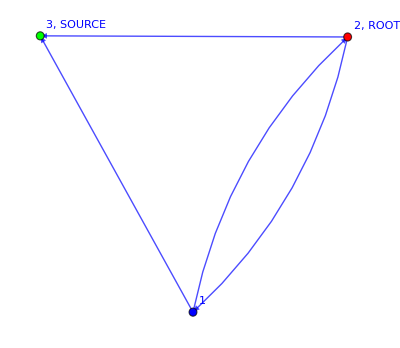

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]]
```

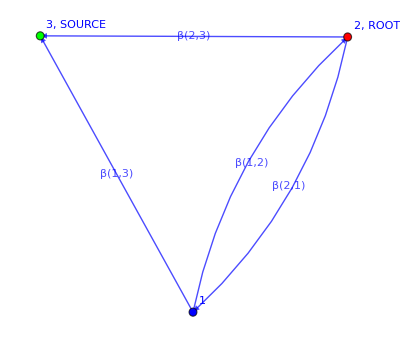

```mathematica
gLabel=MyGraph[edges,root,source,"printEdgesLabel"->True]
```

## DrawOnGraph[]

“Path” should be made of triplets whose first two elements are the initial and final vertices respectively, while the last is the color of this edge

```mathematica
Clear[DrawOnGraph];
Options[DrawOnGraph]={"drawOthers"-> True};
DrawOnGraph[graph_,path__,OptionsPattern[]]:=Module[{locEdges,locPathStyle={},locRoot,locSource,i},
locEdges = EdgeList@graph;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

For[i=1, i<=Length[path],i++,
AppendTo[locPathStyle,{path[[i,1]]->path[[i,2]]->path[[i,3]]}];
(*Print[locPathStyle]*)
];
If[OptionValue["drawOthers"],
(*True*)Graph[locEdges,EdgeStyle->Flatten@{locPathStyle,Blue}, VertexLabels->{locRoot->ToString[locRoot]",ROOT",locSource->ToString[locSource]",SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"],
(*False*)Graph[locEdges,EdgeStyle->Flatten@{locPathStyle,White}, VertexLabels->{locRoot->ToString[locRoot]",ROOT",locSource->ToString[locSource]",SOURCE","Name"}, VertexStyle->{locRoot->Red,locSource->Green,Blue},EdgeShapeFunction->"FilledArrow"]
]
]
```

### Usage example of DrawOnGraph[]

“path” should be an ordered list of pairs of vertices, i.e. edges, that form the desired Laplacian RW

```mathematica
path1={{2,1,Red},{1,3,Green}};
DrawOnGraph[g,path1]
```

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~ROOT].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

Part::partw: Part 1 of PropertyValue[] does not exist.

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~SOURCE].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

General::stop: Further output of PropertyValue::argrx will be suppressed during this calculation.

Part::partw: Part 1 of PropertyValue[] does not exist.

Graph[EdgeList[g],EdgeStyle→{2->1→RGBColor[1, 0, 0],1->3→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},VertexLabels→{PropertyValue[]⟦1⟧→PropertyValue[][[1]] ,ROOT,PropertyValue[]⟦1⟧→PropertyValue[][[1]] ,SOURCE,Name},VertexStyle→{PropertyValue[]⟦1⟧→RGBColor[1, 0, 0],PropertyValue[]⟦1⟧→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

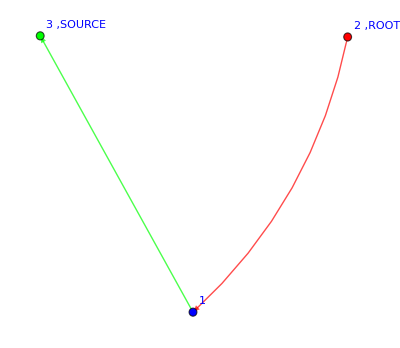

```mathematica
DrawOnGraph[g,path1,"drawOthers"->False]
```

## DrawFromExpression[]

```mathematica
Clear[DrawFromExpression];
Options[DrawFromExpression]={"graph"->g,"drawOthers"->False};

DrawFromExpression[exp_,OptionsPattern[]]:=Module[{terms,graphs={},i},
terms=exp//.R[a_,b_,c_]^n_->R[a,b,c]//Expand;
terms=List @@ (terms+Zeta[3]);
terms=terms//.β[__]->1;
terms=DeleteElements[terms,{Zeta[3]}];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.R[a_,b_,c_]->{a,b,c};
(*For[i=1,i<=Length[terms],i++,
terms[[i]]=DeleteElements[terms[[i]],{a_?NumericQ}];
];*)
Print[terms];

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i,2;;]],"drawOthers"->OptionValue["drawOthers"]]];
Print[graphs[[i]]];
Print[Weight ==terms[[i,1]]];
];
]
```

## AugmentedGraph[]

This is useful to compute the total incoming current from the source towards the DLA cluster/Tree. WE MUST ADD THE EDGE FROM THE OLD SOURCE TO THE NEW SOURCE, AS WELL AS ALLOW THE EDGES FROM THE OLD SOURCE TO THE NEIGHBORS

```mathematica
Clear[AugmentedGraph];
AugmentedGraph[graph_]:=Module[{locVertices,locEdges,locPathStyle={},locRoot,locSource,newSource,oldSourceNeighbors,graphPlus,i},

locVertices = VertexList@graph;
locEdges = EdgeList@graph/.DirectedEdge->List;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

newSource=locVertices[[-1]]+1;

(*Add the edge from the oldSource to the newSource*)
AppendTo[locEdges,{locSource,newSource}];

(*Add all the edges from the oldSource to its neighbors*)
oldSourceNeighbors=Select[locEdges, #[[2]]==locSource &];

For[i=1,i<=Length[oldSourceNeighbors],i++,
AppendTo[locEdges,{locSource,oldSourceNeighbors[[i,1]]}]
];

graphPlus =MyGraph[locEdges,locRoot,newSource,"undirected"->False][[1]];

Return[{graphPlus,locSource,newSource}]
]
```

#### Usage example of AugmentedGraph[]

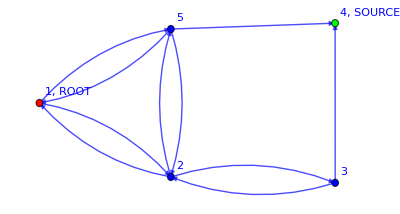

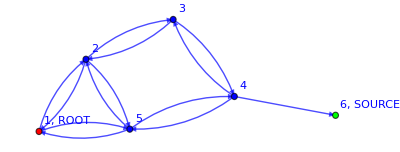
{-Graphics-,4,6}

```mathematica
g=myFavoriteGraph
AugmentedGraph[g]
```

# Field Theory tools

## monoFlatten[]

```mathematica
Clear[monoFlatten];
(*monoFlatten[a_?NumericQ]:={};*)
monoFlatten[a_]:={a};
monoFlatten[{a__}]:={{a}};
monoFlatten[{a__,b__}]:={a,b};
```

#### Test

## ExtractPaths[]

```mathematica
(*To extract the paths and their weights from the expression of an expectation value*)
```

```mathematica
Clear[ExtractPaths];
ExtractPaths[exp_]:=Module[{terms,paths={},i},

terms=exp//Expand;
terms=List @@Collect[terms,R[__,Red]];
terms=Outer[List,terms];

For[i=1,i<=Length[terms],i++,
If[MatchQ[terms[[i,1]],R[__,Red]*A_],
AppendTo[paths,terms[[i]]]
]
];
terms=paths//.R[__,Blue]->1//FullSimplify;

Return[terms]
]
```

#### Usage example of ExtractPaths[]

```mathematica
exp=(1-(Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[β, 2,3] Subscript[β, 3,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]))+(Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[β, 2,3] Subscript[β, 3,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[R, 2,5,RGBColor[0, 0, 1]] Subscript[R, 5,2,RGBColor[0, 0, 1]] Subscript[β, 2,5] Subscript[β, 5,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[R, 5,2,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 2,3] Subscript[β, 3,4] Subscript[β, 5,2])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[0, 0, 1]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[β, 2,5] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[R, 5,4,RGBColor[0, 0, 1]] Subscript[β, 1,5] Subscript[β, 2,3] Subscript[β, 3,2] Subscript[β, 5,4])/((Subscript[β, 1,2]+Subscript[β, 1,5]) (Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4])));ExtractPaths[exp]
```

{{(R_(1,2,RGBColor[1, 0, 0]) β_(1,2) (β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))},{(R_(1,5,RGBColor[1, 0, 0]) β_(1,5) ((β_(2,1)+β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,2)+β_(5,4))))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))}}

## Vertex rules and VertexAssignment[]

The vertices are where the interaction takes place in the field theory.

```mathematica
Clear[V];
V[1.]:=1.;
V[1]:=1;
(*V[0]:=0;*)
V'[a_]:=1
```

```mathematica
Clear[VertexAssignment];
Options[VertexAssignment]={"system"->"LERW","print"->False,"excludedVertices"->{},"sourceBC"->1};

VertexAssignment[graph_,OptionsPattern[]]:=Module[{locVertices,locWeights,totWeights,locSource,action,x,y},
Clear[i];
locVertices=VertexList@graph;
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

(*LERW*)
If[OptionValue["system"]=="LERW",
If[OptionValue["print"],Print["#####   "<>OptionValue["system"]<>"   #####"]];
action = Product[ If[totWeights[[x]]===0 || MemberQ[OptionValue["excludedVertices"],x],1,V[(1+ Sum[locWeights[[x,y]]/totWeights[[x]] χs[y,Subscript[i, x]]χ[x,Subscript[i, x]],{y,Length[locVertices]}] ) ]],{x,Length[locVertices]}];
action*=V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[i, s]])];(*This is the BC*)
Return[action]];

(*DLA*)
If[OptionValue["system"]=="DLA",If[OptionValue["print"],Print["#####   "<>OptionValue["system"]<>"   #####"]];
Return[
Product[ If[totWeights[[x]]===0 || MemberQ[OptionValue["excludedVertices"],x],1,V[(1+ Product[1+locWeights[[x,y]]/totWeights[[x]] χs[y,Subscript[i, x]],{y,Length[locVertices]}] χ[x,Subscript[i, x]]+ Sum[locWeights[[x,y]]/totWeights[[x]] ϕs[y,Subscript[j, x]]ϕ[x,Subscript[j, x]],{y,Length[locVertices]}])] ],{x,Length[locVertices]}]
]]
]
```

### Usage example of VertexAssignment[]

```mathematica
Z=VertexAssignment[g[[1]],"system"->"LERW"]
```

(1+χ[4,i_s]) (1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])) (1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])) (1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4]))

```mathematica
VertexAssignment[g[[1]],"system"->"LERW","excludedVertices"->{1}]
```

(1+χ[4,i_s]) (1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])) (1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4]))

## δrules

```mathematica
ClearAll[Σδrule]
Σδrule={δ[a_,b_]^n_/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,b]^(n-2)δ[a,a],
δ[b_,a_]δ[c_,b_]/;(!NumericQ[b] && !MatchQ[b,Subscript[1, __]]):>δ[c,a],
δ[a_,b_]δ[c_,b_]/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,c],
δ[a_,a_]/;(MatchQ[a,Subscript[i, __]])/;(a=!=Subscript[i, s]):>n,
δ[a_,a_]/;(MatchQ[a,Subscript[k, _]]):>1,
δ[a_,a_]/;(MatchQ[a,Subscript[l, _]]):>1,
δ[a_,a_]/;(MatchQ[a,Subscript[jj, _]]):>1,
δ[a_,a_]/;(MatchQ[a,Subscript[ll, _]]):>1};
```

```mathematica
ClearAll[δruleExternal]
δruleExternal={δ[a_,a_]/;(NumericQ[a] || a==Subscript[i, s] || MatchQ[a,Subscript[j, __]]|| MatchQ[a,Subscript[jj, __]] || MatchQ[a,Subscript[1, __]]||MatchQ[a,Subscript[k, _]]):>1,
δ[a_,b_]/;(NumericQ[a] ||MatchQ[a,Subscript[k, _]]|| MatchQ[a,Subscript[j, __]]|| MatchQ[a,Subscript[jj, __]] || MatchQ[a,Subscript[1, _]])/;(a=!=b):>0,
δ[a_,b_]/;(NumericQ[b] ||MatchQ[b,Subscript[k, _]]|| MatchQ[b,Subscript[j, __]]|| MatchQ[a,Subscript[jj, __]] || MatchQ[b,Subscript[1, _]])/;(a=!=b):>0 };
```

### Usage examples of the δrules

```mathematica
δ[b,a]δ[c,b]/.Σδrule
```

δ[c,a]

```mathematica
δ[b,a]δ[a,b]//.Σδrule
```

n

```mathematica
δ[b,a]δ[c,a]δ[c,b]//.Σδrule
```

n

```mathematica
δ[1,i]δ[i,1]//.Σδrule//.δruleExternal
```

1

```mathematica
δ[1,i]δ[i,2]//.Σδrule//.δruleExternal
```

0

```mathematica
δ[1,i]δ[i,1]δ[a,b]δ[a,b]//.Σδrule//.δruleExternal
```

δ[a,a]

```mathematica
δ[Subscript[k, 1],Subscript[k, 1]]//.Σδrule
```

m

```mathematica
δ[Subscript[i, 1],Subscript[i, 1]]//.Σδrule
```

n

```mathematica
δ[Subscript[j, -1],Subscript[j, -1]]//.δruleExternal
```

1

```mathematica
δ[Subscript[k, -1],Subscript[k, -1]]//.δruleExternal
```

1

```mathematica
δ[Subscript[1, 1],Subscript[1, -1]]δ[Subscript[1, 1],Subscript[1, -1]]//.Σδrule
```

δ[1_1,1_-1]^2

## Operator “vertices” rules

```mathematica
Clear[Op];
Op[1]:=1;
Op[0]:=0;
Op'[_]:=1
```

## FieldsNamesGenerator[]

```mathematica
Clear[FieldsNamesGenerator];
FieldsNamesGenerator[fields_]:=
FieldsNamesGenerator[fields]=Block[{locFields={},starFields={},deltaFields={},deltaStarFields={},l},

locFields=fields;

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]];
];(*End of loop to define the fields*)

Return[{locFields,starFields,deltaFields,deltaStarFields}]
]
```

#### Test

```mathematica
fields={ϕ,χ};
FieldsNamesGenerator[fields]//AbsoluteTiming
FieldsNamesGenerator[fields]//AbsoluteTiming
```

{0.0000616,{{ϕ,χ},{ϕ^*,χ^*},{δϕ,δχ},{δϕs,δχs}}}

{3.1×10^-6,{{ϕ,χ},{ϕ^*,χ^*},{δϕ,δχ},{δϕs,δχs}}}

## WickContractionBlock[]

```mathematica
(*IT SHOULD BE WORKING WITH 4 FIELDS TOO!!!!!*)
```

```mathematica
Clear[WickContractionBlock];
Options[WickContractionBlock]={"print"->False,"fields"->{χ}, "endTime"->1,"#vertices"->10};

WickContractionBlock[A_ +B_,OptionsPattern[]]:=WickContractionBlock[A,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]]+
WickContractionBlock[B,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]];

WickContractionBlock[Op[A_ +B_]*C_,OptionsPattern[]]:=WickContractionBlock[Op[A]C,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]]+
WickContractionBlock[Op[B]C,"print"->OptionValue["print"],"fields"->OptionValue["fields"], "endTime"->OptionValue["endTime"],"#vertices"->OptionValue["#vertices"]];

WickContractionBlock[A_?NumericQ,OptionsPattern[]]:=A;

(*################################################################################
									Partition Function                             
##############################################################################*)
(*There are two possible contributions for each field: 1) it is not contracted: χ->0; 2) it is contracted*)

WickContractionBlock[V[A_] *B_, OptionsPattern[]]:=Block[{locFields={}, starFields={}, deltaFields={},deltaStarFields={},contributions=0,z,zTemp1,zTemp2,κ,j,l,timeIndex},

z=V[A]B;

(*
If[OptionValue["print"],
Print["###################  Partition Function  ##################"];
];*)

(* Updated version with FieldsNamesGenarator
locFields=OptionValue["fields"];

For[l=1,l<=Length[locFields],l++,
AppendTo[starFields, ToExpression[ToString[locFields[[l]]] <> "s"]];
AppendTo[deltaFields, ToExpression["δ"<>ToString[locFields[[l]]] ]];
AppendTo[deltaStarFields,ToExpression["δ"<> ToString[starFields[[l]]] ]]
];(*End of loop to define the fields*)
*)

locFields=OptionValue["fields"][[1]];
starFields=OptionValue["fields"][[2]];
deltaFields=OptionValue["fields"][[3]];
deltaStarFields=OptionValue["fields"][[4]];


(*Start a loop over time*)
For[timeIndex=0,timeIndex<=(OptionValue["endTime"]-1),timeIndex++,

z=z//.f_[x_,Subscript[t, (timeIndex+1)],a_]->f[x,a];

(*Start of loop over fields*)
For[l=1,l<=Length[locFields],l++,

(*Start of loop over space*)
For[j=1,j<=OptionValue["#vertices"],j++,

(*First contribution*)
zTemp1=z//.locFields[[l]][j,a_]->0//.starFields[[l]][j,a_]->0;
If[zTemp1-z=!=0,
contributions=zTemp1;
(*Print["First contribution: ",zTemp1];*)
];

(*Second contribution*)
zTemp1=z/. locFields[[l]][j,a_]->locFields[[l]][j,a]+κ *deltaFields[[l]][j,a];
If[zTemp1-z=!=0,
zTemp1=D[zTemp1,κ]/.κ->0;
];

zTemp2=zTemp1/. starFields[[l]][j,a_]->starFields[[l]][j,a]+κ *deltaStarFields[[l]][j,a];
If[zTemp2-zTemp1=!=0,
zTemp1=D[zTemp2,κ]/.κ->0;
];

zTemp1=Expand[zTemp1];
zTemp2=zTemp1//.deltaFields[[l]][j,a_]*deltaStarFields[[l]][j,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b];

zTemp1=zTemp2/.deltaFields[[l]][j,a_]->0/.deltaStarFields[[l]][j,b_]->0;


If[contributions-zTemp1=!=0,
contributions+=zTemp1;
(*Print["Second contribution: ",zTemp1];*)
];


(*THIRD contribution*)
zTemp1=z/. locFields[[l]][j,a_]->locFields[[l]][j,a]+κ *deltaFields[[l]][j,a];
If[zTemp1-z=!=0,
zTemp1=1/2 D[zTemp1,{κ,2}]/.κ->0;
];

zTemp2=zTemp1/. starFields[[l]][j,a_]->starFields[[l]][j,a]+κ *deltaStarFields[[l]][j,a];
If[zTemp2-zTemp1=!=0,
zTemp1=D[zTemp2,{κ,2}]/.κ->0;
];

zTemp1=Expand[zTemp1];
zTemp2=zTemp1//.deltaFields[[l]][j,a_]*deltaStarFields[[l]][j,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b];
zTemp2=zTemp1//.deltaFields[[l]][j,a_]*deltaStarFields[[l]][j,b_]*deltaFields[[l]][j,a_]*deltaStarFields[[l]][j,b_](*/;(!NumericQ[a*b]):>*)->δ[a,b]*δ[a,b];

zTemp1=zTemp2/.deltaFields[[l]][j,a_]->0/.deltaStarFields[[l]][j,b_]->0;

If[contributions-zTemp1=!=0,
contributions+=zTemp1;
(*Print["Third contribution: ",zTemp1];*)
];

z=contributions;


(*Print["Overall contributions: ",contributions];
Print["################################"];*)

contributions=0;

];(*End of loop over space*)

z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0;

];(*End of loop over fields*)

(*For[l=1,l<=Length[locFields],l++,
z=z/.locFields[[l]][x_,a_]->0;
z=z/.starFields[[l]][x_,a_]->0
];*)

z=z//.Σδrule;

];(*End of loop over time*)

Return[z]
];
```

### WickContractionBlock[] quartic term test

Simple

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
Z=VertexAssignment[g,"system"->"LERW"];
WickContractionBlock[Z ,"fields"->FieldsNamesGenerator[{χ}], "endTime"->1]/.n->-1
WickContractionBlock[Z Subscript[χ, 1,Subscript[i, 10]] Subscript[SuperStar[χ], 1,Subscript[i, 10]],"fields"->FieldsNamesGenerator[{χ}], "endTime"->1]/.n->-1
```

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))

-1+(2 β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))

```mathematica
(*IT SEEMS TO BE WORKING EVEN WITH 4 FIELDS!!!!*)
```

```mathematica
WickContractionBlock[V[ 1+Subscript[χ, 1,Subscript[i, 10]] Subscript[SuperStar[χ], 1,Subscript[i, 10]]] Subscript[χ, 1,Subscript[i, 10]] Subscript[SuperStar[χ], 1,Subscript[i, 10]],"fields"->FieldsNamesGenerator[{χ}], "endTime"->1]
```

3 n

More complex example CORRECT!!

```mathematica
edges={{1,3},{1,2},{2,2},{2,3}};
root=1;
source=3;
g=MyGraph[edges,root,source][[1]];
g;
Z=VertexAssignment[g]
WickContractionBlock[Z,"fields"->{χ}, "endTime"->1]/.n->-1
```

V[1+χ_(3,i_s)] V[1+(β_(1,2) χ_(1,i_1) (χ^*)_(2,i_1))/(β_(1,2)+β_(1,3))+(β_(1,3) χ_(1,i_1) (χ^*)_(3,i_1))/(β_(1,2)+β_(1,3))] V[1+(β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,2)+β_(2,3))+(β_(2,2) χ_(2,i_2) (χ^*)_(2,i_2))/(β_(2,1)+β_(2,2)+β_(2,3))+(β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,2)+β_(2,3))]

1.-(1. β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,2)+β_(2,3)))-(1. β_(2,2))/(β_(2,1)+β_(2,2)+β_(2,3))

Regular 2x2 lattice with absorption (i.e. source) at 4

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source];
g[[1]];
Z=VertexAssignment[g[[1]]]

WickContraction[Z]/.n->-1
```

V[1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3])] V[1+(β[2,1] χ[2,i_2] χs[1,i_2])/(β[2,1]+β[2,4])+(β[2,4] χ[2,i_2] χs[4,i_2])/(β[2,1]+β[2,4])] V[1+(β[3,1] χ[3,i_3] χs[1,i_3])/(β[3,1]+β[3,4])+(β[3,4] χ[3,i_3] χs[4,i_3])/(β[3,1]+β[3,4])]

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

## ExpectationValueBlock[]

```mathematica
Clear[ExpectationValueBlock];
Options[ExpectationValueBlock]={"operator"->1,"print"->False, "fields"->{χ},"endTime"->1,"draw"->False,"graph"->g, "Rrule"->{R[__]->1},"externalδ"->True};

ExpectationValueBlock[Z_,OptionsPattern[]]:=Block[{Nvertices,z,terms,graphs={},i},

Nvertices=Length[VertexList@OptionValue["graph"]];

If[OptionValue["operator"]===1,
(*True*)z=WickContractionBlock[Z,
"print"->OptionValue["print"], 
"fields"->OptionValue["fields"],
"endTime"->OptionValue["endTime"],
"#vertices"->Nvertices
],
(*False*)z=WickContractionBlock[Z*Op[OptionValue["operator"]],
"print"->OptionValue["print"], 
"fields"->OptionValue["fields"],
"endTime"->OptionValue["endTime"],
"#vertices"->Nvertices
]/WickContractionBlock[Z, "fields"->OptionValue["fields"],"endTime"->OptionValue["endTime"],
"#vertices"->Nvertices]
];

If[OptionValue["externalδ"],
z=z//.δruleExternal];
z=z/.n->-1;
z=z/.m->0;

If[OptionValue["draw"],
(*True*)
z=z//.R[a_,b_,c_]^n_->R[a,b,c];
terms=List @@ (z+Zeta[3]);
terms=terms//.β[__]->1;
terms=DeleteElements[terms,{Zeta[3]}];
terms=Outer[List,terms];
terms=terms//.Times->List;
terms=monoFlatten@@@terms;
terms=terms//.R[a_,b_,c_]->{a,b,c};
(*For[i=1,i<=Length[terms],i++,
terms[[i]]=DeleteElements[terms[[i]],{a_?NumericQ}];
];*)
Print[terms];
z=z/.R[___]->1;

For[i=1,i<=Length[terms],i++,
AppendTo[graphs,DrawOnGraph[OptionValue["graph"],terms[[i,2;;]],"drawOthers"->False]];
Print[graphs[[i]]];
Print[Weight ==terms[[i,1]]];
];,

(*False*)z=z/.OptionValue["Rrule"]];

Return[z]]
```

### ExpectationValue[] vs ExpectationValueBlock[] speed test

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
g=myFavoriteGraph;
Z=VertexAssignment[g];
ExpectationValue[Z]//AbsoluteTiming
ExpectationValueBlock[Z,"graph"->g]//AbsoluteTiming
```

{0.0649989,1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))}

{0.0150432,1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))}

It  does  seem  to  be  faster  indeed

## LERWtransitionProb[]

This function computes the transition probability as

```mathematica
Clear[LERWtransitionProb];
Options[LERWtransitionProb]={"draw"->False,"print"->False};

LERWtransitionProb[graph_,path__,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,denominator,prob=1, Z,numerator},
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

If[locRoot =!= path[[1,1]], Print["####  WRONG ROOT  ####"]; Return[NULL]];
If[locSource =!= path[[-1,2]], Print["####  WRONG SOURCE  ####"];Return[NULL]];

Module[{locBC={{},{}},ϕ,i=1,j},
locBC={{ϕ[locSource]==1},{locSource}};

For[i=1,i<=Length[path],i++,

Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]]];
Z=ExpectationValue[Z*χs[path[[i,1]],1]];

If[OptionValue["print"],
Print["#####  Previous Partition Function  #####"];
Print[Z]
];

denominator=Z//FullSimplify;


(*Then we need to solve it again with updated BC at the current step*)

AppendTo[locBC[[1]],ϕ[path[[i,1]]]==0];
AppendTo[locBC[[2]],path[[i,1]]];
(*Print[locBC]*);


Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]],"sourceBC"->denominator^-1];
Z=ExpectationValue[Z*χs[path[[i,2]],1] ];

If[OptionValue["print"],
Print["#####  Current Partition Function  #####"];
Print[Z]
];

numerator=locWeights[[path[[i,1]],path[[i,2]]]]/totWeights[[path[[i,1]]]]*Z//FullSimplify;

Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];
Print[numerator/.β[_,_]->1//FullSimplify];

prob*=numerator//FullSimplify;
]
];
If[OptionValue["draw"],Print[DrawOnGraph[graph,path]]];
Return[prob]
]
```

### Usage example of LaplacianRW[] &LERWtransitionProb[]

“path” should be an ordered list of pairs of vertices, i.e. edges, that form the desired Laplacian RW.
If “draw” is true, then draw the path

Simple cases first

```mathematica
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];

path1={{2,1},{1,3}};
LaplacianRW[g,{{2,1},{1,3}}](*/.β[_,_]->1*)
```

LaplacianRW[-Graphics-,{{2,1},{1,3}}]

```mathematica
(β[1,3] β[2,1])/((β[1,2]+β[1,3]) ((β[1,3] β[2,1])/(β[1,2]+β[1,3])+β[2,3]))//FullSimplify
```

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
%//FullSimplify
```

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
(*Correct!!*)
```

```mathematica
VertexAssignment[g,"excludedVertices"->{2,3}]
LERWtransitionProb[g,path1]
```

(1+χ[3,i_s]) (1+(β[1,2] χ[1,i_1] χs[2,i_1])/(β[1,2]+β[1,3])+(β[1,3] χ[1,i_1] χs[3,i_1])/(β[1,2]+β[1,3]))

#####  Transition probability 2 to 1  #####

1/3

#####  Transition probability 1 to 3  #####

1

(β[1,3] β[2,1])/(β[1,2] β[2,3]+β[1,3] (β[2,1]+β[2,3]))

```mathematica
(*Correct!!*)
```

Let’s try with another example, i.e. my favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
PathFinder[myFavoriteGraph]
```

{{{1,2},{2,3},{3,4}},{{1,2},{2,5},{5,4}},{{1,5},{5,2},{2,3},{3,4}},{{1,5},{5,4}}}

#####  Transition probability 1 to 2  #####

5/11

#####  Transition probability 2 to 3  #####

3/5

#####  Transition probability 3 to 4  #####

1

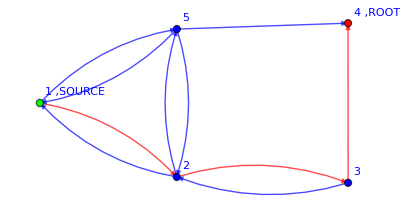

3/11

```mathematica
path2={{1,2},{2,3},{3,4}};
LaplacianRW[myFavoriteGraph,path2,"draw"->True]/.β[_,_]->1
```

```mathematica
LERWtransitionProb[myFavoriteGraph,path2]/.β[_,_]->1
```

#####  Transition probability 1 to 2  #####

5/11

#####  Transition probability 2 to 3  #####

3/5

#####  Transition probability 3 to 4  #####

1

3/11

```mathematica
(*Correct!!!*)
```

# Dynamics

## Znorm[]

```mathematica
Clear[Znorm];
Options[Znorm]={"graph"->g,"fields"->{ϕ,ξ,χ},"theory"->"LERW","βrule"->{β[__]->1.}};

Znorm[expression_,OptionsPattern[]]:=Block[{locZnorm,excludedVertices,token},

excludedVertices=(expression * 2)/.R[__]->1/.γ->1//Expand;
excludedVertices=List @@excludedVertices;
excludedVertices=excludedVertices[[2;;]]; (*Gets rid of the numerical coefficient*)
excludedVertices=excludedVertices/.SuperStar[ϕ][a_,__]->a;
excludedVertices=excludedVertices/.Subscript[(SuperStar[ϕ]), a_,__]^2->a;
excludedVertices=excludedVertices/.SuperStar[ψ][a_,__]->a;
excludedVertices=excludedVertices/.Subscript[(SuperStar[ψ]), a_,__]^n_->a;
excludedVertices=excludedVertices/.SuperStar[ξ][a_,__]->a;
excludedVertices=excludedVertices/.Subscript[(SuperStar[ξ]), a_,__]^n_->a;

locZnorm=VertexAssignment[OptionValue["graph"],"system"->"LERW","excludedVertices"->excludedVertices]/.OptionValue["βrule"];

ExpectationValueBlock[locZnorm * token,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]/.token->1
]
```

#### Test

```mathematica
g
```

-Graphics-

```mathematica
VertexAssignment[g]
```

V[1+χ_(4,i_s)] V[1+(β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(β_(1,2) χ_(1,i_1) (χ^*)_(2,i_1))/(β_(1,2)+β_(1,5))+(β_(1,5) χ_(1,i_1) (χ^*)_(5,i_1))/(β_(1,2)+β_(1,5))] V[1+(β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))]

```mathematica
ExpectationValue[%]
```

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
%/.β[__]->1
```

11/36

```mathematica
Znorm[+5/18 γ Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[SuperStar[ϕ], 2,Subscript[t, 2],Subscript[k, 1]],"graph"->g]
```

0.833333

```mathematica
Znorm[11/18 γ Subscript[SuperStar[ϕ], 1,Subscript[t, 2],Subscript[k, 1]]]
```

13/18

## DynamicLERWaction[]

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”

```mathematica
Clear[DynamicLERWaction];
Options[DynamicLERWaction]={"sourceBC"->1};

DynamicLERWaction[graph_,endTime_,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j];

locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[ If[totWeights[[x]]===0 ,1,(*FALSE*)
V[(1+ Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]ψs[x,Subscript[t, T+1],Subscript[j, -1]]χs[y,Subscript[t, T],1],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]+ ψs[x,Subscript[t, T+1],Subscript[j, -1]]ψ[x,Subscript[t, T],Subscript[j, -1]]) ]],{x,Length[locVertices]}]
V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,endTime}]Product[V[(1+ψ[x,Subscript[t, endTime+1],Subscript[j, -1]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, endTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}];

Return[action]

]
```

### Usage example of DynamicLERWaction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
endTime=1;
DynamicLERWaction[myFavoriteGraph,endTime]
```

V[1+ϕ[1,t_1]] V[1+ϕ[2,t_1]] V[1+ϕ[3,t_1]] V[1+ϕ[5,t_1]] V[1+χ[4,t_1,1]] V[1+ψ[1,t_1]] V[1+ψ[2,t_1]] V[1+ψ[3,t_1]] V[1+ψ[5,t_1]] V[1+(β[3,2] χ[3,t_1,i_3] χs[2,t_1,i_3])/(β[3,2]+β[3,4])+(β[3,4] χ[3,t_1,i_3] χs[4,t_1,i_3])/(β[3,2]+β[3,4])+(β[3,2] ϕ[3,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[3,2]+β[3,4])+ψ[3,t_1] ψs[3,t_2]+(β[3,4] ϕ[3,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[3,2]+β[3,4])] V[1+(β[1,2] χ[1,t_1,i_1] χs[2,t_1,i_1])/(β[1,2]+β[1,5])+(β[1,5] χ[1,t_1,i_1] χs[5,t_1,i_1])/(β[1,2]+β[1,5])+ψ[1,t_1] ψs[1,t_2]+(β[1,2] ϕ[1,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[1,2]+β[1,5])+(β[1,5] ϕ[1,t_1] ϕs[5,t_2] χs[5,t_1,1] ψs[5,t_2])/(β[1,2]+β[1,5])] V[1+(β[2,1] χ[2,t_1,i_2] χs[1,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,3] χ[2,t_1,i_2] χs[3,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,5] χ[2,t_1,i_2] χs[5,t_1,i_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,1] ϕ[2,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[2,1]+β[2,3]+β[2,5])+ψ[2,t_1] ψs[2,t_2]+(β[2,3] ϕ[2,t_1] ϕs[3,t_2] χs[3,t_1,1] ψs[3,t_2])/(β[2,1]+β[2,3]+β[2,5])+(β[2,5] ϕ[2,t_1] ϕs[5,t_2] χs[5,t_1,1] ψs[5,t_2])/(β[2,1]+β[2,3]+β[2,5])] V[1+(β[5,1] χ[5,t_1,i_5] χs[1,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,2] χ[5,t_1,i_5] χs[2,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,4] χ[5,t_1,i_5] χs[4,t_1,i_5])/(β[5,1]+β[5,2]+β[5,4])+(β[5,1] ϕ[5,t_1] ϕs[1,t_2] χs[1,t_1,1] ψs[1,t_2])/(β[5,1]+β[5,2]+β[5,4])+(β[5,2] ϕ[5,t_1] ϕs[2,t_2] χs[2,t_1,1] ψs[2,t_2])/(β[5,1]+β[5,2]+β[5,4])+(β[5,4] ϕ[5,t_1] ϕs[4,t_2] χs[4,t_1,1] ψs[4,t_2])/(β[5,1]+β[5,2]+β[5,4])+ψ[5,t_1] ψs[5,t_2]]

## Evaluation of the DynamicLERWaction[]

Simple case

One time-slice

```mathematica
fields={χ,ϕ,ψ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g;

endTime=1;
Z=DynamicLERWaction[g,endTime];
```

###################  Partition Function  ##################

{{1},{-1/4,{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}}}

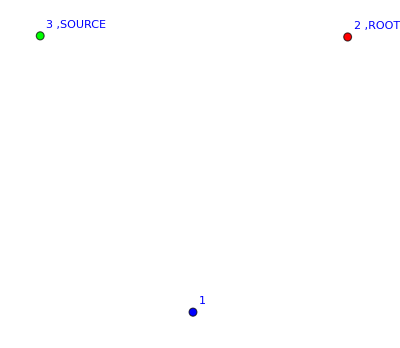

Weight 1

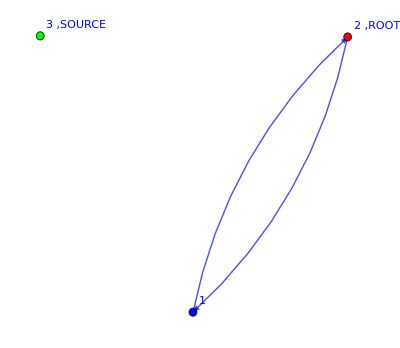

Weight   1
-(-)
  4

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[g,endTime];
ExpectationValue[Z,"fields"->fields,"endTime"->endTime,"print"->False,"draw"->True,"graph"->g]
```

```mathematica
Z//.V[A_]->A;
GeneralizedExpectationValue[%,"draw"->True,"graph"->g]
```

Part::partw: Part 3 of {1,2} does not exist.

Part::partw: Part 3 of {2,1} does not exist.

{-Graphics-,-Graphics-}

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

Two time-slices

```mathematica
endTime=2;
Z=DynamicLERWaction[g,endTime];
Z//.V[A_]->A;
GeneralizedExpectationValue[%]
%/.β[__]->1
```

$Aborted

$Aborted

```mathematica
(*Wich is (Z_t)^2. Correct!!!*)
```

```mathematica
WickContraction[Z,"fields"->fields,"endTime"->endTime]
```

1+V[1+ϕ[1,t_2,0]] V[1+ϕ[2,t_2,0]] V[1+ϕ[3,t_2,0]] V[1+ψ[1,t_2,i_-1]] V[1+ψ[2,t_2,i_-1]] V[1+ψ[3,t_2,i_-1]]+(n R[1,2,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))+(n R[1,2,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] V[1+ϕ[1,t_2,0]] V[1+ϕ[2,t_2,0]] V[1+ϕ[3,t_2,0]] V[1+ψ[1,t_2,i_-1]] V[1+ψ[2,t_2,i_-1]] V[1+ψ[3,t_2,i_-1]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*IT IS WAAAAAY QUICKER!!!!!!!*)
```

```mathematica
ExpectationValue[Z,"fields"->fields,"endTime"->endTime]
```

1+V[1+ϕ[1,t_3,0]] V[1+ϕ[2,t_3,0]] V[1+ϕ[3,t_3,0]] V[1+ψ[1,t_3,i_-1]] V[1+ψ[2,t_3,i_-1]] V[1+ψ[3,t_3,i_-1]]+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(V[1+ϕ[1,t_3,0]] V[1+ϕ[2,t_3,0]] V[1+ϕ[3,t_3,0]] V[1+ψ[1,t_3,i_-1]] V[1+ψ[2,t_3,i_-1]] V[1+ψ[3,t_3,i_-1]] β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))-(2 V[1+ϕ[1,t_3,0]] V[1+ϕ[2,t_3,0]] V[1+ϕ[3,t_3,0]] V[1+ψ[1,t_3,i_-1]] V[1+ψ[2,t_3,i_-1]] V[1+ψ[3,t_3,i_-1]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
%/.V[_]->1
```

2+(2 β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(4 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

Now let’s add an external field

With the generalized expectation value

```mathematica
endTime=1;
Z=DynamicLERWaction[g,endTime];
Z//.V[A_]->A;
GeneralizedExpectationValue[%* ϕs[2,Subscript[t, 1],Subscript[i, -1]]]
```

(β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*Which makes sense since I am not considering any step. endTime=1 means that we consider only one time-slice, i.e. the initial position*)
```

```mathematica
endTime=2;
Z=DynamicLERWaction[g,endTime];
```

```mathematica
(*WARNING: VERY SLOW, DO NOT RUN THIS LINE*)GeneralizedExpectationValue[Z ϕs[2,Subscript[t, 1]]]
```

-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*The previous line gives*)-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))
```

-(4 β[1,2] β[1,3] β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(4 β[1,3] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
%/.β[__]->1
```

3/4

Done with the enhanced WickContraction

###################  Partition Function  ##################

{{},{{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}},{{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}}}

-Graphics-

-Graphics-

-Graphics-

1+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

###################  Operator found  ##################

{{{1,3,RGBColor[0, 0, 1]},{1,3,RGBColor[1, 0, 0]},{2,1,RGBColor[1, 0, 0]}}}

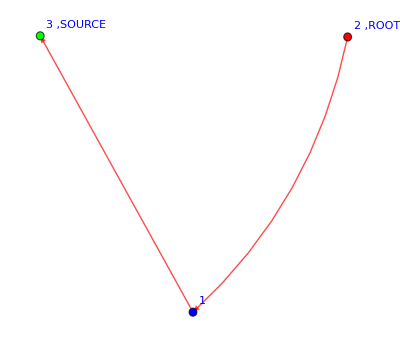

(β[1,3]^2 β[2,1])/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3]))

```mathematica
fields={χ,ϕ,ψ};
endTime=2;
Z=DynamicLERWaction[g,endTime];
ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->True]
Z Op[ϕs[2,Subscript[t, 1],0]];
ExpectationValue[Z Op[ϕs[2,Subscript[t, 1],0]],"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->True]
```

```mathematica
1+V[1+ϕ[1,Subscript[t, 3],0]] V[1+ϕ[2,Subscript[t, 3],0]] V[1+ϕ[3,Subscript[t, 3],0]] V[1+ψ[1,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[2,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[3,Subscript[t, 3],Subscript[i, -1]]]+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)+(V[1+ϕ[1,Subscript[t, 3],0]] V[1+ϕ[2,Subscript[t, 3],0]] V[1+ϕ[3,Subscript[t, 3],0]] V[1+ψ[1,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[2,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[3,Subscript[t, 3],Subscript[i, -1]]] β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))-(2 V[1+ϕ[1,Subscript[t, 3],0]] V[1+ϕ[2,Subscript[t, 3],0]] V[1+ϕ[3,Subscript[t, 3],0]] V[1+ψ[1,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[2,Subscript[t, 3],Subscript[i, -1]]] V[1+ψ[3,Subscript[t, 3],Subscript[i, -1]]] β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))/.f_[a_,Subscript[t, 3],b_]->f[a,b];
WickContraction[V[1]*%,"fields"->fields,"endTime"->0]
```

###################  Partition Function  ##################

###################  Partition Function  ##################

###################  Partition Function  ##################

2+WickContraction[(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2),print→False,fields→{χ,ϕ,ψ},endTime→0]+WickContraction[-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3])),print→False,fields→{χ,ϕ,ψ},endTime→0]+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,3]))

```mathematica
(*expected*)
```

```mathematica
ϕs[2,Subscript[t, 1],0](β[2,1] ϕ[2,Subscript[t, 1],Subscript[k, 2]] ϕs[1,Subscript[t, 2],Subscript[k, 2]] χs[1,Subscript[t, 1],1] ψs[2,Subscript[t, 2],Subscript[i, -1]])/(β[2,1]+β[2,3])((β[1,3] χ[1,Subscript[t, 1],Subscript[i, 1]] χs[3,Subscript[t, 1],Subscript[i, 1]])/(β[1,2]+β[1,3])χ[3,Subscript[t, 1],1])((β[1,3] ϕ[1,Subscript[t, 2],Subscript[k, 1]] ϕs[3,Subscript[t, 3],Subscript[k, 1]] χs[3,Subscript[t, 2],1] ψs[1,Subscript[t, 3],Subscript[i, -1]])/(β[1,2]+β[1,3])ϕ[3,Subscript[t, 3],0]ψ[1,Subscript[t, 3],Subscript[i, -1]]χ[3,Subscript[t, 2],1])ψ[2,Subscript[t, 2],Subscript[i, -1]]ψs[2,Subscript[t, 3],Subscript[i, -1]]ψ[2,Subscript[t, 3],Subscript[i, -1]]
```

```mathematica
(*Weight*)
```

```mathematica
ϕs[2,Subscript[t, 1],0](β[2,1] ϕ[2,Subscript[t, 1],Subscript[k, 2]] ϕs[1,Subscript[t, 2],Subscript[k, 2]] χs[1,Subscript[t, 1],1] ψs[2,Subscript[t, 2],Subscript[i, -1]])/(β[2,1]+β[2,3])((β[1,3] χ[1,Subscript[t, 1],Subscript[i, 1]] χs[3,Subscript[t, 1],Subscript[i, 1]])/(β[1,2]+β[1,3])χ[3,Subscript[t, 1],1])((β[1,3] ϕ[1,Subscript[t, 2],Subscript[k, 1]] ϕs[3,Subscript[t, 3],Subscript[k, 1]] χs[3,Subscript[t, 2],1] ψs[1,Subscript[t, 3],Subscript[i, -1]])/(β[1,2]+β[1,3])ϕ[3,Subscript[t, 3],0]ψ[1,Subscript[t, 3],Subscript[i, -1]]χ[3,Subscript[t, 2],1])ψ[2,Subscript[t, 2],Subscript[i, -1]]ψs[2,Subscript[t, 3],Subscript[i, -1]]ψ[2,Subscript[t, 3],Subscript[i, -1]]//.f_[_,_,_]->1
```

(β[1,3]^2 β[2,1])/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,3]))

```mathematica
(*THEY SEEM TO MATCH!!!!!!!!!*)
```

Regular 2x2 lattice with absorption (i.e. source) at 4

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source][[1]];
g;
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[g,endTime]
```

V[1+ϕ[1,t_2,0]] V[1+ϕ[2,t_2,0]] V[1+ϕ[3,t_2,0]] V[1+ϕ[4,t_2,0]] V[1+χ[4,t_1,1]] V[1+ψ[1,t_2,j_-1]] V[1+ψ[2,t_2,j_-1]] V[1+ψ[3,t_2,j_-1]] V[1+ψ[4,t_2,j_-1]] V[1+(R[1,2,RGBColor[0, 0, 1]] β[1,2] χ[1,t_1,i_1] χs[2,t_1,i_1])/(β[1,2]+β[1,3])+(R[1,3,RGBColor[0, 0, 1]] β[1,3] χ[1,t_1,i_1] χs[3,t_1,i_1])/(β[1,2]+β[1,3])+(R[1,2,RGBColor[1, 0, 0]] β[1,2] ϕ[1,t_1,k_1] ϕs[2,t_2,k_1] χs[2,t_1,1] ψs[1,t_2,j_-1])/(β[1,2]+β[1,3])+(R[1,3,RGBColor[1, 0, 0]] β[1,3] ϕ[1,t_1,k_1] ϕs[3,t_2,k_1] χs[3,t_1,1] ψs[1,t_2,j_-1])/(β[1,2]+β[1,3])+ψ[1,t_1,j_-1] ψs[1,t_2,j_-1]] V[1+(R[2,1,RGBColor[0, 0, 1]] β[2,1] χ[2,t_1,i_2] χs[1,t_1,i_2])/(β[2,1]+β[2,4])+(R[2,4,RGBColor[0, 0, 1]] β[2,4] χ[2,t_1,i_2] χs[4,t_1,i_2])/(β[2,1]+β[2,4])+(R[2,1,RGBColor[1, 0, 0]] β[2,1] ϕ[2,t_1,k_2] ϕs[1,t_2,k_2] χs[1,t_1,1] ψs[2,t_2,j_-1])/(β[2,1]+β[2,4])+(R[2,4,RGBColor[1, 0, 0]] β[2,4] ϕ[2,t_1,k_2] ϕs[4,t_2,k_2] χs[4,t_1,1] ψs[2,t_2,j_-1])/(β[2,1]+β[2,4])+ψ[2,t_1,j_-1] ψs[2,t_2,j_-1]] V[1+(R[3,1,RGBColor[0, 0, 1]] β[3,1] χ[3,t_1,i_3] χs[1,t_1,i_3])/(β[3,1]+β[3,4])+(R[3,4,RGBColor[0, 0, 1]] β[3,4] χ[3,t_1,i_3] χs[4,t_1,i_3])/(β[3,1]+β[3,4])+(R[3,1,RGBColor[1, 0, 0]] β[3,1] ϕ[3,t_1,k_3] ϕs[1,t_2,k_3] χs[1,t_1,1] ψs[3,t_2,j_-1])/(β[3,1]+β[3,4])+(R[3,4,RGBColor[1, 0, 0]] β[3,4] ϕ[3,t_1,k_3] ϕs[4,t_2,k_3] χs[4,t_1,1] ψs[3,t_2,j_-1])/(β[3,1]+β[3,4])+ψ[3,t_1,j_-1] ψs[3,t_2,j_-1]]

```mathematica
Z/.V[A_]->A/.R[___]->1;
GeneralizedExpectationValue[%]
```

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source][[1]];
g;
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[g,endTime];

ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->False]
```

###################  Partition Function  ##################

1-(β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))-(β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))

Two time-slices (it’s very slow, I would need kay’s trick for the vertices AND NOW I HAVE IT!!!!)

```mathematica
edges={{1,2},{1,3},{2,4},{3,4}};
root=1;
source=4;
g=MyGraph[edges,root,source][[1]];
g;
fields={χ,ϕ,ψ};
endTime=2;
Z=DynamicLERWaction[g,endTime];
ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->False]
```

###################  Partition Function  ##################

1+(β[1,2]^2 β[2,1]^2)/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,4])^2)-(2 β[1,2] β[2,1])/((β[1,2]+β[1,3]) (β[2,1]+β[2,4]))+(β[1,3]^2 β[3,1]^2)/((β[1,2]+β[1,3])^2 (β[3,1]+β[3,4])^2)-(2 β[1,3] β[3,1])/((β[1,2]+β[1,3]) (β[3,1]+β[3,4]))+(2 β[1,2] β[1,3] β[2,1] β[3,1])/((β[1,2]+β[1,3])^2 (β[2,1]+β[2,4]) (β[3,1]+β[3,4]))

My favorite graph

Partition function

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]];
```

```mathematica
fields={χ,ϕ,ψ};
endTime=1;
Z=DynamicLERWaction[myFavoriteGraph,endTime];

ExpectationValue[Z ,"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->False]
```

###################  Partition Function  ##################

1-(β[1,2] β[2,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]))-(β[2,3] β[3,2])/((β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]))-(β[1,5] β[5,1])/((β[1,2]+β[1,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,2] β[2,5] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))+(β[1,5] β[2,3] β[3,2] β[5,1])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4]))-(β[1,5] β[2,1] β[5,2])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))-(β[2,5] β[5,2])/((β[2,1]+β[2,3]+β[2,5]) (β[5,1]+β[5,2]+β[5,4]))

With a source at 1:

###################  Operator found  ##################

{{{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{2,3,RGBColor[1, 0, 0]},{3,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]},{5,2,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[0, 0, 1]},{2,5,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]},{5,4,RGBColor[1, 0, 0]}},{{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]},{2,5,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}},{{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{2,5,RGBColor[1, 0, 0]},{3,4,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}}}

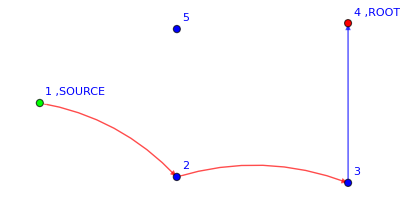

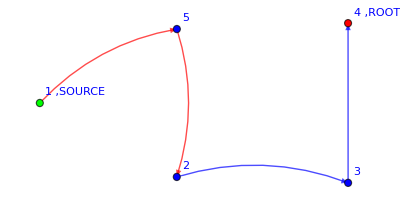

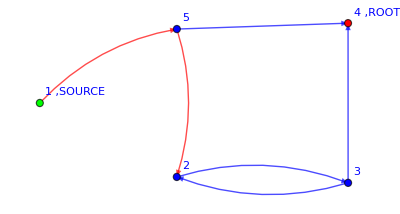

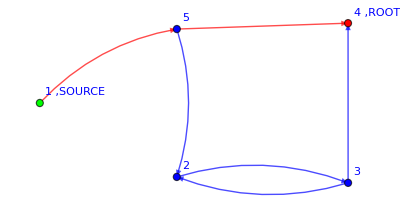

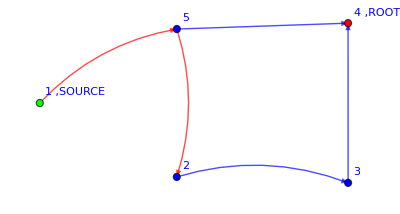

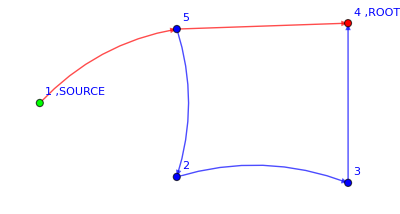

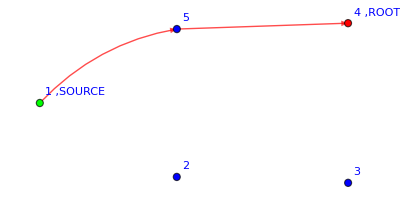

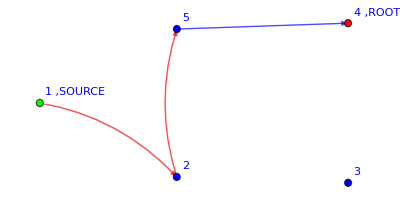

-Graphics-

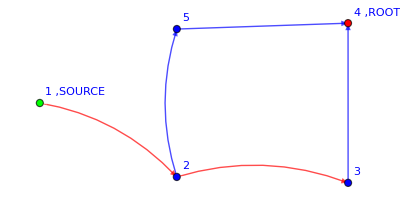

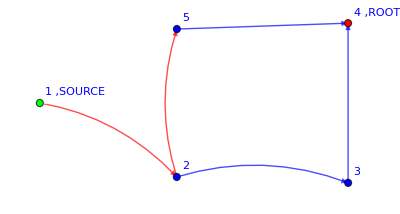

(β[1,2] β[2,3]^2 β[3,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2)+(β[1,5] β[2,3]^2 β[3,4]^2 β[5,2]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2 (β[5,1]+β[5,2]+β[5,4])^2)-(2 β[1,5] β[2,3]^2 β[3,2] β[3,4] β[5,2] β[5,4])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2 (β[5,1]+β[5,2]+β[5,4])^2)+(2 β[1,5] β[2,3] β[3,4] β[5,2] β[5,4])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4])^2)+(β[1,5] β[5,4]^2)/((β[1,2]+β[1,5]) (β[5,1]+β[5,2]+β[5,4])^2)+(β[1,2] β[2,5]^2 β[5,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[5,1]+β[5,2]+β[5,4])^2)+(β[1,5] β[2,3]^2 β[3,2]^2 β[5,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4])^2 (β[5,1]+β[5,2]+β[5,4])^2)-(2 β[1,5] β[2,3] β[3,2] β[5,4]^2)/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5]) (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4])^2)+(2 β[1,2] β[2,3] β[2,5] β[3,4] β[5,4])/((β[1,2]+β[1,5]) (β[2,1]+β[2,3]+β[2,5])^2 (β[3,2]+β[3,4]) (β[5,1]+β[5,2]+β[5,4]))

```mathematica
g=myFavoriteGraph;
fields={χ,ϕ,ψ};
endTime=2;
Z=DynamicLERWaction[g,endTime];
Z Op[ϕs[1,Subscript[t, 1],0]];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"fields"->fields,"endTime"->endTime,"graph"->g,"draw"->True]
```

## DynamicDLAaction[]

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”.

```mathematica
Clear[DynamicDLAaction];
Options[DynamicDLAaction]={"sourceBC"->1,"excludedVertices"->{}};

DynamicDLAaction[graph_,endTime_,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j];

locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[ If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,(*FALSE*)
V[(1+ Sum[locWeights[[x,y]]R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]ϕs[x,Subscript[t, T+1],Subscript[k, x]]χs[y,Subscript[t, T],1],{y,Length[locVertices]}]+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]+ ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]) ]],{x,Length[locVertices]}]
V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,endTime}]Product[V[(1+ϕ[x,Subscript[t, endTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, endTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}];

Return[action]

]
```

### Usage example of DynamicDLAaction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Partition Function

###################  Partition Function  ##################

{{1},{-1/6,{1,2,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]}},{-1/6,{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]}},{-1/6,{1,5,RGBColor[0, 0, 1]},{5,1,RGBColor[0, 0, 1]}},{-1/18,{1,2,RGBColor[0, 0, 1]},{2,5,RGBColor[0, 0, 1]},{5,1,RGBColor[0, 0, 1]}},{1/36,{1,5,RGBColor[0, 0, 1]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,1,RGBColor[0, 0, 1]}},{-1/18,{1,5,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}},{-1/9,{2,5,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}}}

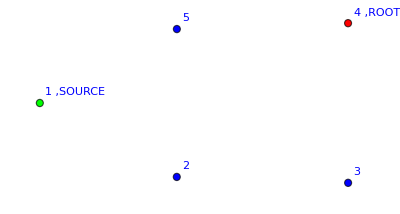

Weight==1

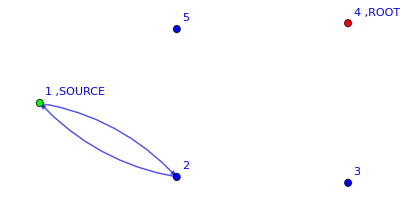

Weight==-1/6

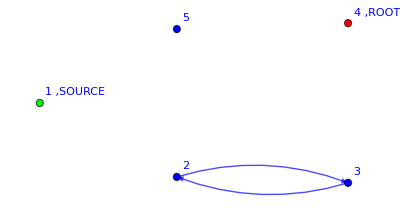

Weight==-1/6

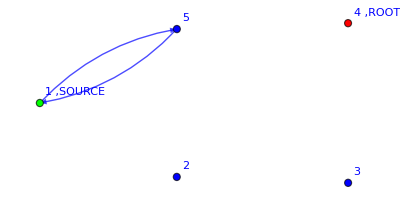

Weight==-1/6

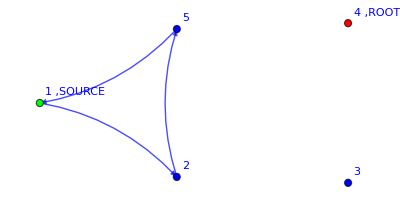

Weight==-1/18

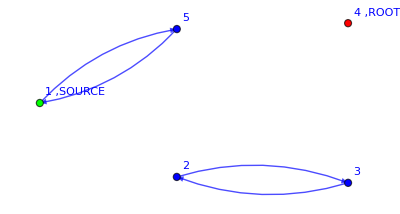

Weight==1/36

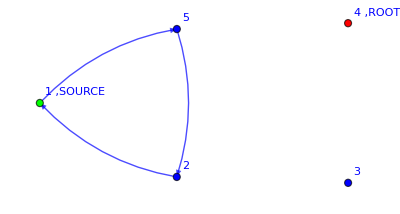

Weight==-1/18

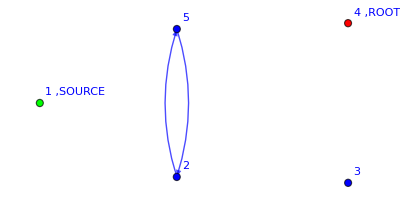

Weight==-1/9

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->True]
```

Observables: Op[ϕs[1,t_1,0]]

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

Here I would like to compare it to the result obtained by solving the laplace eq but I still need the normalization from the FT

```mathematica
sol=LaplaceEqSolver[g];
phi2=Select[sol,#[[1]]==Φ[2] &][[1,2]];
phi5=Select[sol,#[[1]]==Φ[5] &][[1,2]];
phi2/(phi2+phi5)//FullSimplify
phi5/(phi2+phi5)//FullSimplify
```

(β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4)))/((β_(2,1)+2 β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+2 (β_(5,2)+β_(5,4))))

((β_(2,1)+β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,2)+β_(5,4)))/((β_(2,1)+2 β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+2 (β_(5,2)+β_(5,4))))

Observables: Op[χs[1,t_1,1]], i.e. the solution to the Laplace eq

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[g,endTime];
ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Partition Function  ##################

((R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
g=AugmentedGraph[myFavoriteGraph]
Z=DynamicDLAaction[g,endTime];

ExpectationValue[Z  ,"endTime"->endTime,"fields"->fields,"draw"->False]
```

-Graphics-

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))+(β_(1,2) β_(2,1) β_(3,4) β_(4,3))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(3,4) β_(4,3) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,2) β_(2,5) β_(3,4) β_(4,3) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,3) β_(3,4) β_(4,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,1) β_(3,4) β_(4,3) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(3,2) β_(4,3) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,2) β_(2,1) β_(4,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

Φ evaluated at the new source:

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Which is the same as Z. CORRECT!*)
```

Φ evaluated at the old source			 CORRECT!!!!!

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

###################  Operator found  ##################

(β_(4,6))/(β_(4,3)+β_(4,5)+β_(4,6))-(β_(2,3) β_(3,2) β_(4,6))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(4,6) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Let's check that we get the same result by solving the Laplace equation. First, we need to properly normalize it, i.e. divide by Z*)
```

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Phi4FT=ExpectationValue[Z  ,"operator"->χs[4,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Partition Function  ##################

((β_(4,6))/(β_(4,3)+β_(4,5)+β_(4,6))-(β_(2,3) β_(3,2) β_(4,6))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(4,6) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
(*Now from the Laplace eq*)
```

```mathematica
Phi4Laplace=LaplaceEqSolver[g,"selectSolution"->4]
```

(β_(4,6) (β_(2,1) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4)))/(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,6) β_(5,1)+β_(2,5) β_(3,2) β_(4,6) β_(5,1)+β_(2,1) β_(3,4) β_(4,6) β_(5,1)+β_(2,3) β_(3,4) β_(4,6) β_(5,1)+β_(2,5) β_(3,4) β_(4,6) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,6) β_(5,2)+β_(2,1) β_(3,4) β_(4,6) β_(5,2)+β_(2,3) β_(3,4) β_(4,6) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4)+β_(2,1) β_(3,2) β_(4,6) β_(5,4)+β_(2,5) β_(3,2) β_(4,6) β_(5,4)+β_(2,1) β_(3,4) β_(4,6) β_(5,4)+β_(2,3) β_(3,4) β_(4,6) β_(5,4)+β_(2,5) β_(3,4) β_(4,6) β_(5,4))

```mathematica
(*And now, let's subtract them*)
```

```mathematica
Phi4Laplace-Phi4FT//FullSimplify
```

0

```mathematica
(*CORRECT!!!!!!!!*)
```

### Let’s check that kay’s trick for the total current works: IT WORKS ONLY FOR SYMMETRICAL β BUT WITH ANY σ!!!!!!

```mathematica
g=AugmentedGraph[myFavoriteGraph];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Limit[σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

```mathematica
Z2=DynamicDLAaction[myFavoriteGraph,endTime,"excludedVertices"->{1}];
ExpectationValue[Z2  Op[χs[2,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]+
ExpectationValue[Z2  Op[χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]-

ExpectationValue[Z2  Op[χs[2,Subscript[t, 1],1]+χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Operator found  ##################

###################  Operator found  ##################

0

```mathematica
(*Ok, I can insert the operators directly inside Op[]*)
```

Kay’s trick works only with symmetrical weights!!!!!

```mathematica
(*Now let's verify that kay's trick works*)
```

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Limit[σ*(ExpectationValue[Z  ,"operator"->(χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]

Z2=DynamicDLAaction[myFavoriteGraph,endTime,"excludedVertices"->{1}];
ExpectationValue[Z2,"operator"-> (β[1,2]χs[2,Subscript[t, 1],1]+β[1,5]χs[5,Subscript[t, 1],1]),"endTime"->endTime,"fields"->fields,"draw"->False]
%%%-%//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

###################  Operator found  ##################

###################  Partition Function  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

###################  Operator found  ##################

###################  Partition Function  ##################

((β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

(β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)-β_(1,5) β_(2,3) β_(3,4) β_(5,2)-β_(1,5) (β_(2,5) β_(3,2)+(β_(2,3)+β_(2,5)) β_(3,4)) β_(5,4)+β_(2,1) ((β_(3,2) β_(4,3)+(β_(3,2)+β_(3,4)) β_(4,5)) (β_(5,1)+β_(5,2))-(β_(1,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))+β_(1,2) (-β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)-β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))))/(β_(2,5) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,4))+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))+β_(2,1) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Limit[σ*(ExpectationValue[Z Op[(χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1])],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]

Z2=DynamicDLAaction[myFavoriteGraph,endTime,"excludedVertices"->{1}];
ExpectationValue[Z2 Op[(β[1,2]χs[2,Subscript[t, 1],1]+β[1,5]χs[5,Subscript[t, 1],1])],"endTime"->endTime,"fields"->fields,"draw"->False]
%%%-%//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

###################  Operator found  ##################

(β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

(β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)-β_(1,5) β_(2,3) β_(3,4) β_(5,2)-β_(1,5) (β_(2,5) β_(3,2)+(β_(2,3)+β_(2,5)) β_(3,4)) β_(5,4)+β_(2,1) ((β_(3,2) β_(4,3)+(β_(3,2)+β_(3,4)) β_(4,5)) (β_(5,1)+β_(5,2))-(β_(1,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))+β_(1,2) (-β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)-β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4))))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

Does it work for any σ? YESSS

```mathematica
g
```

-Graphics-

Exclude just 1: CORRECT!!!!

```mathematica
AugmGraph=AugmentedGraph[myFavoriteGraph];
g=AugmGraph[[1]];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
exp1=(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ)
exp2=(ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ)
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

###################  Operator found  ##################

σ/(σ+β_(4,3)+β_(4,5))-(σ β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(σ β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp2/.σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])*A_+σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])*B_+σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])->HoldForm[σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])*(A+B+1)]
```

(σ (-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+1))/(σ+β_(4,3)+β_(4,5))

```mathematica
σ (exp1-exp2)
```

σ (1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-σ/(σ+β_(4,3)+β_(4,5))+(σ β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
Limit[σ (exp1-exp2), σ -> ∞]-((-(Subscript[β, 3,4] Subscript[β, 4,3])/((Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]))+(Subscript[β, 2,5] Subscript[β, 3,4] Subscript[β, 4,3] Subscript[β, 5,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[β, 2,3] Subscript[β, 3,4] Subscript[β, 4,5] Subscript[β, 5,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[β, 2,5] Subscript[β, 3,2] Subscript[β, 4,3] Subscript[β, 5,4])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))-(Subscript[β, 4,5] Subscript[β, 5,4])/((σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4]))+(Subscript[β, 2,3] Subscript[β, 3,2] Subscript[β, 4,5] Subscript[β, 5,4])/((Subscript[β, 2,1]+Subscript[β, 2,3]+Subscript[β, 2,5]) (Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]) (Subscript[β, 5,1]+Subscript[β, 5,2]+Subscript[β, 5,4])))(σ+Subscript[β, 4,3]+Subscript[β, 4,5])+exp2(σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5]))^-1(Subscript[β, 4,3]+Subscript[β, 4,5]))//FullSimplify
```

0

```mathematica
(*CORRECT!!! THE LIMIT σ->∞ IS THE SAME AS THE BIG PARENTHESES. CHECK ONENOTE NOTEBOOK FOR DETAILS*)
```

```mathematica
Limit[σ(1-σ/(σ+Subscript[β, 4,3]+Subscript[β, 4,5])),σ->∞]
```

β_(4,3)+β_(4,5)

```mathematica
Limit[σ((Subscript[β, 3,4] Subscript[β, 4,3])/((Subscript[β, 3,2]+Subscript[β, 3,4]) (σ+Subscript[β, 4,3]+Subscript[β, 4,5]))),σ->∞]
```

(β_(3,4) β_(4,3))/(β_(3,2)+β_(3,4))

```mathematica
exp3=ExpectationValue[Z Op[β[1,2]χs[2,Subscript[t, 1],1]+β[1,5]χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ
```

###################  Operator found  ##################

(σ β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))+(σ β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(1,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(σ β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
σ(exp1-exp2)-exp3//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

(σ (β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)-β_(1,5) β_(2,3) β_(3,4) β_(5,2)-β_(1,5) (β_(2,5) β_(3,2)+(β_(2,3)+β_(2,5)) β_(3,4)) β_(5,4)+β_(2,1) ((β_(3,2) β_(4,3)+(β_(3,2)+β_(3,4)) β_(4,5)) (β_(5,1)+β_(5,2))-(β_(1,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))+β_(1,2) (-β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)-β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4)))))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

Exclude 1 and 2: CORRECT!!!!

```mathematica
AugmGraph=AugmentedGraph[myFavoriteGraph];
g=AugmGraph[[1]];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1,2}];
exp1=σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ)
```

###################  Operator found  ##################

σ (1-σ/(σ+β_(4,3)+β_(4,5))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))-(β_(4,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
exp2=ExpectationValue[Z Op[β[2,3]χs[3,Subscript[t, 1],1]+(β[1,5]+β[2,5])χs[5,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ
```

###################  Operator found  ##################

(σ β_(2,3) β_(3,4))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)))+(σ β_(1,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(σ β_(2,5) β_(5,4))/((σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp1-exp2//FullSimplify
%//.β[a_,b_]/;(a<b):>β[b,a]//FullSimplify
```

-(σ (β_(3,4) (β_(2,3)-β_(4,5))-β_(3,2) (β_(4,3)+β_(4,5))) (β_(5,1)+β_(5,2))+σ (β_(2,3) β_(3,4)+β_(1,5) (β_(3,2)+β_(3,4))+β_(2,5) (β_(3,2)+β_(3,4))-β_(3,2) β_(4,3)) β_(5,4))/((β_(3,2)+β_(3,4)) (σ+β_(4,3)+β_(4,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

0

### β or β/r? Answer: β!!

We want to check whether we need to use β or β/r in the DLA dynamical action

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
g=AugmentedGraph[myFavoriteGraph];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
DLAnorm=Limit[σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

```mathematica
g=myFavoriteGraph;
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
exp=ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]/DLAnorm/.β[__]->1
ExtractPaths[exp](*This is nicely normalized!!!*)
```

###################  Operator found  ##################

18/11 (1-1/6 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1])+1/6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])-1/9 R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/18 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])+1/9 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1])-1/18 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]))

{{18/11},{-3/11,{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]}},{3/11,{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]}},{-2/11,{2,5,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}},{1/11,{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]},{5,2,RGBColor[0, 0, 1]}},{6/11,{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[0, 0, 1]}},{2/11,{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}},{-1/11,{1,5,RGBColor[1, 0, 0]},{2,3,RGBColor[0, 0, 1]},{3,2,RGBColor[0, 0, 1]},{5,4,RGBColor[0, 0, 1]}}}

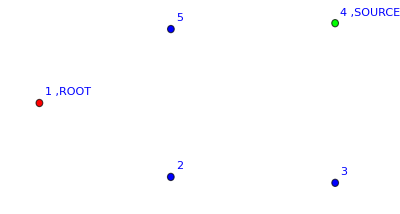

Weight==18/11

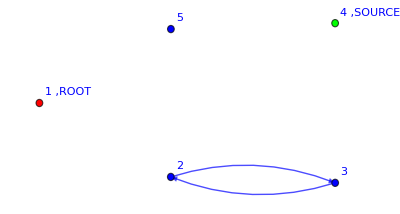

Weight==-3/11

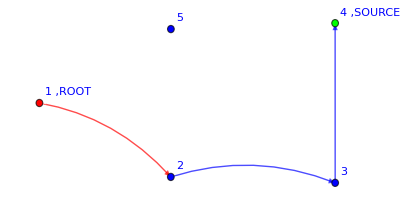

Weight==3/11

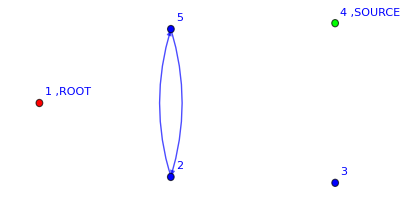

Weight==-2/11

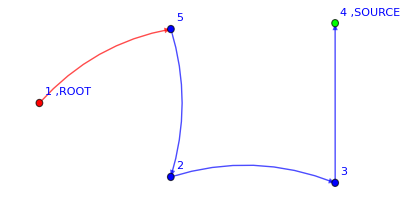

Weight==1/11

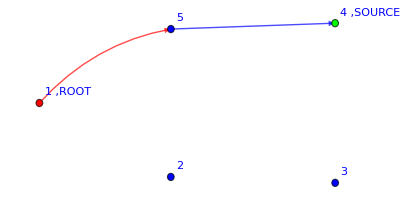

Weight==6/11

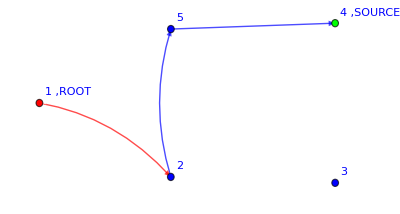

Weight==2/11

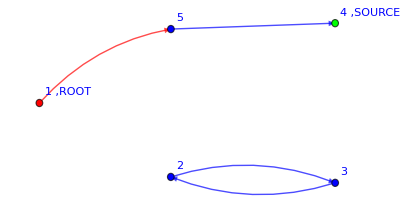

Weight==-1/11

```mathematica
DrawFromExpression[exp];
```

Now, if we use β/r: NOT PROPERLY NORMALIZED

```mathematica
g=AugmentedGraph[myFavoriteGraph];
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
DLAnorm=Limit[σ(ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]-χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]/.Subscript[β, 4,6]->σ),σ->∞]
```

###################  Operator found  ##################

(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4))/(β_(2,1) β_(3,2) β_(5,1)+β_(2,3) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,3) β_(3,2) β_(5,2)+β_(2,5) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,5) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,3) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4))

```mathematica
g=myFavoriteGraph;
endTime=1;
fields={ϕ,χ};
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
exp=ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]/DLAnorm/.β[__]->1
ExtractPaths[exp]
```

###################  Operator found  ##################

18/11 (1-1/6 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1])+1/12 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])-1/9 R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/36 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])+1/6 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])+1/18 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1])-1/36 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]))

{{(5 R_(1,2,RGBColor[1, 0, 0]))/22},{(3 R_(1,5,RGBColor[1, 0, 0]))/11}}

```mathematica
(*Not properly normalized!!!*)
```

### Can I send each field to zero immediately or do I need to do it at the end? Answer: YESSS!

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Partition Function right away

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

Partition function field by field

```mathematica
fields={ϕ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
fields={χ};
ExpectationValue[%%,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

V[1+χ_(4,1)] V[1+(β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(β_(1,2) χ_(1,i_1) (χ^*)_(2,i_1))/(β_(1,2)+β_(1,5))+(β_(1,5) χ_(1,i_1) (χ^*)_(5,i_1))/(β_(1,2)+β_(1,5))] V[1+(β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))]

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Ok, for the partition funciton it works. But in the partition function only χ is used*)
```

Observables: Op[ϕs[1,t_1,0]]

Right away

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Operator found  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

Field by field

```mathematica
fields={ϕ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[myFavoriteGraph,endTime];
ExpectationValue[Z Op[ϕs[1,Subscript[t, 1],0]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
fields={χ};
ExpectationValue[%%,"endTime"->endTime,"fields"->fields,"draw"->False"Rrule"->{}]
```

###################  Operator found  ##################

V[1+χ_(4,1)] V[1+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))]+R_(1,2,RGBColor[1, 0, 0]) V[1+χ_(4,1)] V[1+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))] β_(1,2) (χ^*)_(2,1)+R_(1,5,RGBColor[1, 0, 0]) V[1+χ_(4,1)] V[1+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,i_3) (χ^*)_(2,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,i_3) (χ^*)_(4,i_3))/(β_(3,2)+β_(3,4))] V[1+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,i_5) (χ^*)_(1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,i_5) (χ^*)_(2,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,i_5) (χ^*)_(4,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,i_2) (χ^*)_(1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,i_2) (χ^*)_(3,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,i_2) (χ^*)_(5,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))] β_(1,5) (χ^*)_(5,1)

###################  Partition Function  ##################

###################  Partition Function  ##################

###################  Partition Function  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*OK!! IT SEEMS THAT I CAN DO FIRST A FIELD, SET TO ZERO, THEN THE OTHERS*)
```

## I would like to compute the denominator of the DLA transition probability. To do this, I try to use nn different fields and then send nn->-1.

```mathematica
fields={χ,ϕ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g=AugmentedGraph[g];

endTime=1;Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}]
```

V[1+ϕ_(1,t_2,0)] V[1+ϕ_(1,t_2,k_1)] V[1+ϕ_(2,t_2,0)] V[1+ϕ_(2,t_2,k_2)] V[1+ϕ_(3,t_2,0)] V[1+ϕ_(3,t_2,k_3)] V[1+ϕ_(4,t_2,0)] V[1+ϕ_(4,t_2,k_4)] V[1+χ_(4,t_1,1)] V[1+ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1)+R_(1,2,RGBColor[1, 0, 0]) β_(1,2) ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (χ^*)_(2,t_1,1)+(R_(1,2,RGBColor[0, 0, 1]) β_(1,2) χ_(1,t_1,i_1) (χ^*)_(2,t_1,i_1))/(β_(1,2)+β_(1,3))+R_(1,3,RGBColor[1, 0, 0]) β_(1,3) ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (χ^*)_(3,t_1,1)+(R_(1,3,RGBColor[0, 0, 1]) β_(1,3) χ_(1,t_1,i_1) (χ^*)_(3,t_1,i_1))/(β_(1,2)+β_(1,3))] V[1+ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2)+R_(2,1,RGBColor[1, 0, 0]) β_(2,1) ϕ_(2,t_1,k_2) (ϕ^*)_(1,t_2,k_2) (ϕ^*)_(2,t_2,k_2) (χ^*)_(1,t_1,1)+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,t_1,i_2) (χ^*)_(1,t_1,i_2))/(β_(2,1)+β_(2,3))+R_(2,3,RGBColor[1, 0, 0]) β_(2,3) ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(3,t_2,k_2) (χ^*)_(3,t_1,1)+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,t_1,i_2) (χ^*)_(3,t_1,i_2))/(β_(2,1)+β_(2,3))] V[1+ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3)+R_(3,1,RGBColor[1, 0, 0]) β_(3,1) ϕ_(3,t_1,k_3) (ϕ^*)_(1,t_2,k_3) (ϕ^*)_(3,t_2,k_3) (χ^*)_(1,t_1,1)+(R_(3,1,RGBColor[0, 0, 1]) β_(3,1) χ_(3,t_1,i_3) (χ^*)_(1,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+R_(3,2,RGBColor[1, 0, 0]) β_(3,2) ϕ_(3,t_1,k_3) (ϕ^*)_(2,t_2,k_3) (ϕ^*)_(3,t_2,k_3) (χ^*)_(2,t_1,1)+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,t_1,i_3) (χ^*)_(2,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+R_(3,4,RGBColor[1, 0, 0]) β_(3,4) ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3) (ϕ^*)_(4,t_2,k_3) (χ^*)_(4,t_1,1)+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,t_1,i_3) (χ^*)_(4,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))]

```mathematica
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))-(β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,2) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,3) β_(2,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
ExpectationValue[Z Op[(χs[4,Subscript[t, 1],1]-χs[3,Subscript[t, 1],1])]Op[(χs[4,Subscript[t, 1],1]-χs[3,Subscript[t, 1],1])],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

0

```mathematica
fields={χ,ϕ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g=AugmentedGraph[g];

endTime=1;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];

Z1=ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))-(β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,2) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(1,3) β_(2,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
endTime=3;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
Z3=ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Partition Function  ##################

1-(β_(1,2)^3 β_(2,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3)+(3 β_(1,2)^2 β_(2,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2)-(3 β_(1,2) β_(2,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)))-(β_(1,3)^3 β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(β_(1,2)^3 β_(2,3)^3 β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2)^2 β_(1,3) β_(2,3)^2 β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2) β_(1,3)^2 β_(2,3) β_(3,1)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2)^2 β_(1,3) β_(2,1) β_(2,3)^2 β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2)^2 β_(2,3)^3 β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,2) β_(1,3)^2 β_(2,1) β_(2,3) β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,2) β_(1,3) β_(2,3)^2 β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^3 β_(2,1) β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^2 β_(2,3) β_(3,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2) β_(1,3)^2 β_(2,1)^2 β_(2,3) β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,2) β_(1,3) β_(2,1) β_(2,3)^2 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,2) β_(2,3)^3 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^3 β_(2,1)^2 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(6 β_(1,3)^2 β_(2,1) β_(2,3) β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3) β_(2,3)^2 β_(3,1) β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(β_(1,3)^3 β_(2,1)^3 β_(3,2)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3)^2 β_(2,1)^2 β_(2,3) β_(3,2)^3)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(3 β_(1,3) β_(2,1) β_(2,3)^2 β_(3,2)^3)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)-(β_(2,3)^3 β_(3,2)^3)/((β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(3 β_(1,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2)^3 β_(2,1) β_(2,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2)^2 β_(1,3) β_(2,1) β_(2,3) β_(3,1)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(3 β_(1,2)^2 β_(2,3)^2 β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2) β_(1,3)^2 β_(2,1) β_(3,1)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,2) β_(1,3) β_(2,3) β_(3,1)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2)^2 β_(1,3) β_(2,1)^2 β_(2,3) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2)^2 β_(2,1) β_(2,3)^2 β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2) β_(1,3)^2 β_(2,1)^2 β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,2) β_(2,3)^2 β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,3)^2 β_(2,1) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,3) β_(2,3) β_(3,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2) β_(1,3)^2 β_(2,1)^3 β_(3,2)^2)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(6 β_(1,2) β_(1,3) β_(2,1)^2 β_(2,3) β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,2) β_(2,1) β_(2,3)^2 β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(3 β_(1,3)^2 β_(2,1)^2 β_(3,2)^2)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(6 β_(1,3) β_(2,1) β_(2,3) β_(3,2)^2)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)+(3 β_(2,3)^2 β_(3,2)^2)/((β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)-(3 β_(1,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^3 β_(2,1)^2 β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^2 β_(1,3) β_(2,1)^2 β_(3,1))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2)^2 β_(2,1) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2) β_(1,3) β_(2,1) β_(3,1))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2) β_(2,3) β_(3,1))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^2 β_(1,3) β_(2,1)^3 β_(3,2))/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,2)^2 β_(2,1)^2 β_(2,3) β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2) β_(1,3) β_(2,1)^2 β_(3,2))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))+(6 β_(1,2) β_(2,1) β_(2,3) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(1,3) β_(2,1) β_(3,2))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))-(3 β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
Z1^3-Z3//FullSimplify
```

0

```mathematica
(*SO, USING nn TIME-SLICES YIELDS Z^nn!!!! THIS IS EXPECTED. DOES IT WORK FOR <χ^*χ>?? *)
```

Does it work for <χ^*χ>?

###################  Operator found  ##################

{{1/12,{1,3,RGBColor[0, 0, 1]},{2,1,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]}},{1/6,{2,3,RGBColor[0, 0, 1]},{3,4,RGBColor[0, 0, 1]}}}

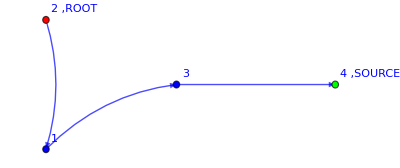

Weight==1/12

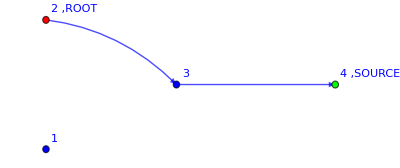

Weight==1/6

(β_(1,3) β_(2,1) β_(3,4))/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))+(β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)) (β_(3,1)+β_(3,2)+β_(3,4)))

```mathematica
fields={χ,ϕ};
edges = {{1,2},{2,3},{3,1}};
root=2;
source=3;
g=MyGraph[edges,root,source][[1]];
g=AugmentedGraph[g];

endTime=1;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];

Z1=ExpectationValue[Z Op[χs[2,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->True,"graph"->g]
```

```mathematica
endTime=3;
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{}];
Z3=ExpectationValue[Z Op[χs[2,Subscript[t, 1],1]] Op[χs[2,Subscript[t, 2],1]] Op[χs[2,Subscript[t, 3],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

(β_(1,3)^3 β_(2,1)^3 β_(3,4)^3)/((β_(1,2)+β_(1,3))^3 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(3 β_(1,3)^2 β_(2,1)^2 β_(2,3) β_(3,4)^3)/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(3 β_(1,3) β_(2,1) β_(2,3)^2 β_(3,4)^3)/((β_(1,2)+β_(1,3)) (β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)+(β_(2,3)^3 β_(3,4)^3)/((β_(2,1)+β_(2,3))^3 (β_(3,1)+β_(3,2)+β_(3,4))^3)

```mathematica
Z1^3-Z3//FullSimplify
```

0

```mathematica
(*IT WORKS!!!!!!!!!!!
CAN I USE THIS TO COMPUTE THE DENOMINATOR?????*)
```

Other attempt

```mathematica
Z=V[1+(Subscript[R, 1,2,RGBColor[0, 0, 1]] Subscript[β, 1,2] Subscript[χ, 1,Subscript[t, 1],Subscript[i, 1]] Subscript[SuperStar[χ], 2,Subscript[t, 1],Subscript[i, 1]])/(Subscript[β, 1,2]+Subscript[β, 1,3])+(Subscript[R, 1,3,RGBColor[0, 0, 1]] Subscript[β, 1,3] Subscript[χ, 1,Subscript[t, 1],Subscript[i, 1]] Subscript[SuperStar[χ], 3,Subscript[t, 1],Subscript[i, 1]])/(Subscript[β, 1,2]+Subscript[β, 1,3])] V[1+(Subscript[R, 2,1,RGBColor[0, 0, 1]] Subscript[β, 2,1] Subscript[χ, 2,Subscript[t, 1],Subscript[i, 2]] Subscript[SuperStar[χ], 1,Subscript[t, 1],Subscript[i, 2]])/(Subscript[β, 2,1]+Subscript[β, 2,3])+(Subscript[R, 2,3,RGBColor[0, 0, 1]] Subscript[β, 2,3] Subscript[χ, 2,Subscript[t, 1],Subscript[i, 2]] Subscript[SuperStar[χ], 3,Subscript[t, 1],Subscript[i, 2]])/(Subscript[β, 2,1]+Subscript[β, 2,3])] V[1+(Subscript[R, 3,1,RGBColor[0, 0, 1]] Subscript[β, 3,1] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3]] Subscript[SuperStar[χ], 1,Subscript[t, 1],Subscript[i, 3]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])+(Subscript[R, 3,2,RGBColor[0, 0, 1]] Subscript[β, 3,2] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3]] Subscript[SuperStar[χ], 2,Subscript[t, 1],Subscript[i, 3]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])+(Subscript[R, 3,4,RGBColor[0, 0, 1]] Subscript[β, 3,4] Subscript[χ, 3,Subscript[t, 1],Subscript[i, 3]] Subscript[SuperStar[χ], 4,Subscript[t, 1],Subscript[i, 3]])/(Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])];Z=Z/.χ[a_,b_,c_]->(ϕ[a,b,c])/.χs[a_,b_,c_]->ϕs[a,b,c]
```

V[1+(R_(1,2,RGBColor[0, 0, 1]) β_(1,2) ϕ_(1,t_1,i_1) (ϕ^*)_(2,t_1,i_1))/(β_(1,2)+β_(1,3))+(R_(1,3,RGBColor[0, 0, 1]) β_(1,3) ϕ_(1,t_1,i_1) (ϕ^*)_(3,t_1,i_1))/(β_(1,2)+β_(1,3))] V[1+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) ϕ_(2,t_1,i_2) (ϕ^*)_(1,t_1,i_2))/(β_(2,1)+β_(2,3))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) ϕ_(2,t_1,i_2) (ϕ^*)_(3,t_1,i_2))/(β_(2,1)+β_(2,3))] V[1+(R_(3,1,RGBColor[0, 0, 1]) β_(3,1) ϕ_(3,t_1,i_3) (ϕ^*)_(1,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) ϕ_(3,t_1,i_3) (ϕ^*)_(2,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) ϕ_(3,t_1,i_3) (ϕ^*)_(4,t_1,i_3))/(β_(3,1)+β_(3,2)+β_(3,4))]

```mathematica
fields={χ,ϕ};
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]-(1-(Subscript[β, 1,2] Subscript[β, 2,1])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 2,1]+Subscript[β, 2,3]))-(Subscript[β, 1,3] Subscript[β, 3,1])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[β, 1,2] Subscript[β, 2,3] Subscript[β, 3,1])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 2,1]+Subscript[β, 2,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[β, 1,3] Subscript[β, 2,1] Subscript[β, 3,2])/((Subscript[β, 1,2]+Subscript[β, 1,3]) (Subscript[β, 2,1]+Subscript[β, 2,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4]))-(Subscript[β, 2,3] Subscript[β, 3,2])/((Subscript[β, 2,1]+Subscript[β, 2,3]) (Subscript[β, 3,1]+Subscript[β, 3,2]+Subscript[β, 3,4])))^2//FullSimplify
```

###################  Partition Function  ##################

(2 β_(1,3)^2 β_(3,2) (-2 β_(2,3) (β_(2,1)+β_(2,3)) β_(3,1)-β_(2,1)^2 β_(3,2))-2 β_(1,2)^2 β_(2,3) (β_(2,3) β_(3,1)^2+2 β_(2,1) β_(3,2) (β_(3,1)+β_(3,2)+β_(3,4)))-4 β_(1,2) β_(1,3) β_(2,3) β_(3,2) (β_(2,3) β_(3,1)+β_(2,1) (3 β_(3,1)+β_(3,2)+β_(3,4))))/((β_(1,2)+β_(1,3))^2 (β_(2,1)+β_(2,3))^2 (β_(3,1)+β_(3,2)+β_(3,4))^2)

# Final Dynamical theories (?)

## FinalDynamicLERWaction[]

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”

```mathematica
Clear[FinalDynamicLERWaction];
Options[FinalDynamicLERWaction]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

FinalDynamicLERWaction[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[ 
V[(1+γ Sum[If[totWeights[[x]]===0 ,0,(*FALSE*)locWeights[[x,y]]/totWeights[[x]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]ψs[x,Subscript[t, T+1],Subscript[j, -1]]- ϕs[x,Subscript[t, T+1],Subscript[k, x]])ϕ[x,Subscript[t, T],Subscript[k, x]]χs[y,Subscript[t, T],1]] ,{y,Length[locVertices]}]+Sum[If[totWeights[[x]]===0 ,0,(*FALSE*)locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]]],{y,Length[locVertices]}]+ ψs[x,Subscript[t, T+1],Subscript[j, -1]]ψ[x,Subscript[t, T],Subscript[j, -1]]+ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]) ],{x,Length[locVertices]}]
V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,locStartingTime,locEndTime}]Product[V[(1+ψ[x,Subscript[t, locEndTime+1],Subscript[j, -1]])(*This allows the PASSIVE path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],Subscript[k, x]])(*This allows the ACTIVE path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}];

Return[action]

]
```

```mathematica
fields={ϕ,ψ,χ};
startingTime=1;
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicLERWaction["graph"->g,"startingTime"->startingTime,"endTime"->endTime];
ExpectationValue[Z Op[Subscript[SuperStar[ϕ], 2,Subscript[t, 1],0] Subscript[SuperStar[ψ], 1,Subscript[t, 1],Subscript[j, -1]]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Operator found  ##################

1-(γ R_(3,4,RGBColor[0, 0, 1]) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) β_(2,3) β_(3,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(γ R_(5,4,RGBColor[0, 0, 1]) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(2,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
%/.β[__]->1/.R[__,Blue]->1
```

1-(5 γ)/18+1/6 γ R_(2,3,RGBColor[1, 0, 0])+1/9 γ R_(2,5,RGBColor[1, 0, 0])

### Usage example of DynamicLERWaction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Partition Function

```mathematica
g=myFavoriteGraph;
endTime=1;
Z=FinalDynamicLERWaction["graph"->g,"endTime"->endTime]
```

V[1+ϕ_(1,t_2,0)] V[1+ϕ_(2,t_2,0)] V[1+ϕ_(3,t_2,0)] V[1+ϕ_(4,t_2,0)] V[1+ϕ_(5,t_2,0)] V[1+ψ_(1,t_2,j_-1)] V[1+ψ_(2,t_2,j_-1)] V[1+ψ_(3,t_2,j_-1)] V[1+ψ_(4,t_2,j_-1)] V[1+ψ_(5,t_2,j_-1)] V[1+ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1)+(R_(1,2,RGBColor[0, 0, 1]) β_(1,2) χ_(1,t_1,i_1) (χ^*)_(2,t_1,i_1))/(β_(1,2)+β_(1,5))+(R_(1,5,RGBColor[0, 0, 1]) β_(1,5) χ_(1,t_1,i_1) (χ^*)_(5,t_1,i_1))/(β_(1,2)+β_(1,5))+ψ_(1,t_1,j_-1) (ψ^*)_(1,t_2,j_-1)+γ ((R_(1,2,RGBColor[1, 0, 0]) β_(1,2) ϕ_(1,t_1,k_1) χ_(4,t_1,1) (χ^*)_(2,t_1,1) (-(ϕ^*)_(1,t_2,k_1)+(ϕ^*)_(2,t_2,k_1) (ψ^*)_(1,t_2,j_-1)))/(β_(1,2)+β_(1,5))+(R_(1,5,RGBColor[1, 0, 0]) β_(1,5) ϕ_(1,t_1,k_1) χ_(4,t_1,1) (χ^*)_(5,t_1,1) (-(ϕ^*)_(1,t_2,k_1)+(ϕ^*)_(5,t_2,k_1) (ψ^*)_(1,t_2,j_-1)))/(β_(1,2)+β_(1,5)))] V[1+ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2)+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,t_1,i_2) (χ^*)_(1,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,t_1,i_2) (χ^*)_(3,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,t_1,i_2) (χ^*)_(5,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+ψ_(2,t_1,j_-1) (ψ^*)_(2,t_2,j_-1)+γ ((R_(2,1,RGBColor[1, 0, 0]) β_(2,1) ϕ_(2,t_1,k_2) χ_(4,t_1,1) (χ^*)_(1,t_1,1) (-(ϕ^*)_(2,t_2,k_2)+(ϕ^*)_(1,t_2,k_2) (ψ^*)_(2,t_2,j_-1)))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[1, 0, 0]) β_(2,3) ϕ_(2,t_1,k_2) χ_(4,t_1,1) (χ^*)_(3,t_1,1) (-(ϕ^*)_(2,t_2,k_2)+(ϕ^*)_(3,t_2,k_2) (ψ^*)_(2,t_2,j_-1)))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,5,RGBColor[1, 0, 0]) β_(2,5) ϕ_(2,t_1,k_2) χ_(4,t_1,1) (χ^*)_(5,t_1,1) (-(ϕ^*)_(2,t_2,k_2)+(ϕ^*)_(5,t_2,k_2) (ψ^*)_(2,t_2,j_-1)))/(β_(2,1)+β_(2,3)+β_(2,5)))] V[1+ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3)+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,t_1,i_3) (χ^*)_(2,t_1,i_3))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,t_1,i_3) (χ^*)_(4,t_1,i_3))/(β_(3,2)+β_(3,4))+ψ_(3,t_1,j_-1) (ψ^*)_(3,t_2,j_-1)+γ ((R_(3,2,RGBColor[1, 0, 0]) β_(3,2) ϕ_(3,t_1,k_3) χ_(4,t_1,1) (χ^*)_(2,t_1,1) (-(ϕ^*)_(3,t_2,k_3)+(ϕ^*)_(2,t_2,k_3) (ψ^*)_(3,t_2,j_-1)))/(β_(3,2)+β_(3,4))+(R_(3,4,RGBColor[1, 0, 0]) β_(3,4) ϕ_(3,t_1,k_3) χ_(4,t_1,1) (χ^*)_(4,t_1,1) (-(ϕ^*)_(3,t_2,k_3)+(ϕ^*)_(4,t_2,k_3) (ψ^*)_(3,t_2,j_-1)))/(β_(3,2)+β_(3,4)))] V[1+ϕ_(5,t_1,k_5) (ϕ^*)_(5,t_2,k_5)+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,t_1,i_5) (χ^*)_(1,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,t_1,i_5) (χ^*)_(2,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,t_1,i_5) (χ^*)_(4,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+ψ_(5,t_1,j_-1) (ψ^*)_(5,t_2,j_-1)+γ ((R_(5,1,RGBColor[1, 0, 0]) β_(5,1) ϕ_(5,t_1,k_5) χ_(4,t_1,1) (χ^*)_(1,t_1,1) (-(ϕ^*)_(5,t_2,k_5)+(ϕ^*)_(1,t_2,k_5) (ψ^*)_(5,t_2,j_-1)))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[1, 0, 0]) β_(5,2) ϕ_(5,t_1,k_5) χ_(4,t_1,1) (χ^*)_(2,t_1,1) (-(ϕ^*)_(5,t_2,k_5)+(ϕ^*)_(2,t_2,k_5) (ψ^*)_(5,t_2,j_-1)))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,4,RGBColor[1, 0, 0]) β_(5,4) ϕ_(5,t_1,k_5) χ_(4,t_1,1) (χ^*)_(4,t_1,1) (-(ϕ^*)_(5,t_2,k_5)+(ϕ^*)_(4,t_2,k_5) (ψ^*)_(5,t_2,j_-1)))/(β_(5,1)+β_(5,2)+β_(5,4)))]

Observable Op[ϕs[1,t_1,0]]

```mathematica
fields={ϕ,ψ,χ};
startingTime=1;
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicLERWaction["graph"->g,"startingTime"->startingTime,"endTime"->endTime];
exp=ExpectationValue[Z Op[Subscript[SuperStar[ϕ], 1,Subscript[t, 1],0]],"endTime"->endTime+1,"fields"->fields,"draw"->False,"Rrule"->{}]

(*Dexp=D[exp,γ]/.γ->0*)
```

###################  Operator found  ##################

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp*18/13/.β[__]->1/.R[__,Blue]->1/.γ->2 γ//Expand
```

1-(11 γ)/13+5/13 γ R_(1,2,RGBColor[1, 0, 0])+6/13 γ R_(1,5,RGBColor[1, 0, 0])

```mathematica
%/.R[__,Red]->1
```

1

```mathematica
(*Dexp=D[exp,γ]/.γ->0;*)
exp2=exp/.R[a_,b_,Red]->R[a,b,Red]Op[ϕs[b,Subscript[t, 1],0]ψs[a,Subscript[t, 1],Subscript[j, -1]]]
```

1-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp=ExpectationValue[Z exp2,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Partition Function  ##################

1-(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))+(R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 β_(2,3)^2 β_(3,2)^2)/((β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(γ R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3)^2 β_(3,2) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)-(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,3)^2 β_(3,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,3)^2 β_(3,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(1,2) β_(2,1) β_(2,3) β_(3,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)))-(2 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2)^2 β_(2,1) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1])^2 R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(2,5)^2 β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,5) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,3)^2 β_(3,2) β_(3,4) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(2,5) β_(3,2) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3) β_(2,5) β_(3,4) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,3) β_(3,4) β_(5,1) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])^2 β_(1,5) β_(2,1) β_(2,5) β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(2,5,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1])^2 β_(2,5)^2 β_(5,2)^2)/((β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])^2 β_(1,5)^2 β_(2,1) β_(2,3) β_(3,4) β_(5,2)^2)/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1])^2 β_(1,5) β_(2,3) β_(2,5) β_(3,4) β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1])^2 R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2)^2 β_(2,5)^2 β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,5) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,5) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,3)^2 β_(3,2)^2 β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3) β_(2,5) β_(3,2) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3) β_(2,5) β_(3,2) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(2 γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,3) β_(3,2) β_(5,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(2,5) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(2,5,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,1) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,5) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5)^2 β_(2,1) β_(2,3) β_(3,2) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(2,5) β_(3,2) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,5)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,5)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(2 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(2 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3) β_(3,2) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)-(R_(1,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,1))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(2 R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2)^2 β_(2,3) β_(2,5) β_(3,4) β_(5,1))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,3) β_(3,4) β_(5,1))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(2,1) β_(2,5) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(2 R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,1) β_(2,3) β_(3,2) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(2 R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,3) β_(2,5) β_(3,2) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2)^2 β_(2,1) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(1,5) β_(2,1) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5))^2 (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(2 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(2 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
comp=exp*18/13/.β[__]->1/.R[__,Blue]->1/.γ->2 γ//Expand
```

11/36-(121 γ)/468+5/13 γ R_(1,2,RGBColor[1, 0, 0])-25/117 γ^2 R_(1,2,RGBColor[1, 0, 0])+5/13 γ R_(1,5,RGBColor[1, 0, 0])-4/13 γ^2 R_(1,5,RGBColor[1, 0, 0])+5/39 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0])+10/117 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0])+2/39 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+10/39 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

```mathematica
comp/.γ^n_->γ
```

11/36-(121 γ)/468+20/117 γ R_(1,2,RGBColor[1, 0, 0])+1/13 γ R_(1,5,RGBColor[1, 0, 0])+5/39 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0])+10/117 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0])+2/39 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+10/39 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

```mathematica
Dexp=D[exp,γ]/.γ->0;
exp2=Dexp/.R[a_,b_,Red]R[b_,c_,Red]->R[a,b,Red]R[b,c,Red]Op[ϕs[c,Subscript[t, 1],0]ψs[b,Subscript[t, 1],Subscript[j, -1]]ψs[a,Subscript[t, 1],Subscript[j, -1]]]
```

(Op[(ϕ^*)_(3,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,3)^2 β_(3,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,5)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,2)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(2 Op[(ϕ^*)_(4,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,5) β_(2,3) β_(3,2) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(3,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
exp=ExpectationValue[Z exp2,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Partition Function  ##################

(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,3)^2 β_(3,4)^3)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^3)+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,3)^2 β_(3,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2)+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,5)^2 β_(5,4)^3)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^3)+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^3 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^3 β_(3,4)^3 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^3 (β_(3,2)+β_(3,4))^3 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(2,3,RGBColor[1, 0, 0]) R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^3 β_(3,2) β_(3,4)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^3 (β_(3,2)+β_(3,4))^3 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,2) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 β_(1,2) β_(2,5)^2 β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4)^2 β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
Dexp=D[exp,γ]/.γ->0;
exp2=Dexp/.R[a_,b_,Red]R[b_,c_,Red]R[c_,d_,Red]->R[a,b,Red]R[b,c,Red]R[c,d,Red]Op[ϕs[c,Subscript[t, 1],0]ψs[c,Subscript[t, 1],Subscript[j, -1]]ψs[b,Subscript[t, 1],Subscript[j, -1]]ψs[a,Subscript[t, 1],Subscript[j, -1]]]
```

(Op[(ϕ^*)_(3,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(3,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 R_(3,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,3)^2 β_(3,4)^3)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^3)+(Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1])^2 R_(5,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,5)^2 β_(5,4)^3)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(5,1)+β_(5,2)+β_(5,4))^3)+(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^3 R_(5,2,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(1,5) β_(2,3)^3 β_(3,4)^3 β_(5,2)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^3 (β_(3,2)+β_(3,4))^3 (β_(5,1)+β_(5,2)+β_(5,4))^2)-(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1])^2 R_(2,3,RGBColor[1, 0, 0]) R_(3,2,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^3 β_(3,2) β_(3,4)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^3 (β_(3,2)+β_(3,4))^3 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(2,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1])^2 R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3)^2 β_(3,4)^2 β_(5,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(5,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(5,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(1,2) β_(2,3) β_(2,5) β_(3,4) β_(5,4)^2)/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))^2)+(Op[(ϕ^*)_(3,t_1,0) (ψ^*)_(1,t_1,j_-1) (ψ^*)_(2,t_1,j_-1) (ψ^*)_(3,t_1,j_-1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(2,5) β_(3,4)^2 β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5))^2 (β_(3,2)+β_(3,4))^2 (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
ExpectationValue[Z Op[Subscript[SuperStar[ϕ], 2,Subscript[t, 1],0] Subscript[SuperStar[ψ], 1,Subscript[t, 1],Subscript[j, -1]]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{}]
```

###################  Operator found  ##################

1

```mathematica
exp/.R[__,Blue]->1/.β[__]->1
```

169/324+25/648 γ R_(1,2,RGBColor[1, 0, 0])+1/54 γ R_(1,5,RGBColor[1, 0, 0])

```mathematica
%/.γ->1/.R[__]->1
```

125/216

## FinalDynamicDLAaction[] THIS IS OUR BENCHMARK

This action should be:

For fields that do not have a color index, we default to set it to j_-1, because in the WickContraction[] it automated with color indices.
Instead, the source is set with index 1, so that it can contract with an external “probe”.

```mathematica
Clear[FinalDynamicDLAaction];
Options[FinalDynamicDLAaction]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"endTime"->10};

FinalDynamicDLAaction[OptionsPattern[]]:=Module[{locGraph,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];

locGraph=OptionValue["graph"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, x]]-1)ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]χs[y,Subscript[t, T],1],{y,Length[locVertices]}]+
Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]+ ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]]) ]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]
(*V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]*);

action=Product[actionTimeSlice[T],{T,locEndTime}](*Product[V[(1+ϕ[x,Subscript[t, locEndTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}]*);

Return[action]

]
```

### Usage example of DynamicDLAaction[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Partition Function

```mathematica
Z=FinalDynamicDLAaction["graph"->g,"endTime"->endTime]
```

V[1+ϕ_(4,t_1,k_4) (ϕ^*)_(4,t_2,k_4)+χ_(4,t_1,1)] V[1+ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3)+(R_(3,2,RGBColor[0, 0, 1]) β_(3,2) χ_(3,t_1,i_3) (χ^*)_(2,t_1,i_3))/(β_(3,2)+β_(3,4))+γ (β_(3,2) ϕ_(3,t_1,k_3) (-1+R_(3,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_3)) (ϕ^*)_(3,t_2,k_3) (χ^*)_(2,t_1,1)+β_(3,4) ϕ_(3,t_1,k_3) (ϕ^*)_(3,t_2,k_3) (-1+R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(4,t_2,k_3)) (χ^*)_(4,t_1,1))+(R_(3,4,RGBColor[0, 0, 1]) β_(3,4) χ_(3,t_1,i_3) (χ^*)_(4,t_1,i_3))/(β_(3,2)+β_(3,4))] V[1+ϕ_(5,t_1,k_5) (ϕ^*)_(5,t_2,k_5)+(R_(5,1,RGBColor[0, 0, 1]) β_(5,1) χ_(5,t_1,i_5) (χ^*)_(1,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+(R_(5,2,RGBColor[0, 0, 1]) β_(5,2) χ_(5,t_1,i_5) (χ^*)_(2,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))+γ (β_(5,1) ϕ_(5,t_1,k_5) (-1+R_(5,1,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_5)) (ϕ^*)_(5,t_2,k_5) (χ^*)_(1,t_1,1)+β_(5,2) ϕ_(5,t_1,k_5) (-1+R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_5)) (ϕ^*)_(5,t_2,k_5) (χ^*)_(2,t_1,1)+β_(5,4) ϕ_(5,t_1,k_5) (-1+R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(4,t_2,k_5)) (ϕ^*)_(5,t_2,k_5) (χ^*)_(4,t_1,1))+(R_(5,4,RGBColor[0, 0, 1]) β_(5,4) χ_(5,t_1,i_5) (χ^*)_(4,t_1,i_5))/(β_(5,1)+β_(5,2)+β_(5,4))] V[1+ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1)+(R_(1,2,RGBColor[0, 0, 1]) β_(1,2) χ_(1,t_1,i_1) (χ^*)_(2,t_1,i_1))/(β_(1,2)+β_(1,5))+γ (β_(1,2) ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1) (-1+R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(2,t_2,k_1)) (χ^*)_(2,t_1,1)+β_(1,5) ϕ_(1,t_1,k_1) (ϕ^*)_(1,t_2,k_1) (-1+R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(5,t_2,k_1)) (χ^*)_(5,t_1,1))+(R_(1,5,RGBColor[0, 0, 1]) β_(1,5) χ_(1,t_1,i_1) (χ^*)_(5,t_1,i_1))/(β_(1,2)+β_(1,5))] V[1+ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2)+(R_(2,1,RGBColor[0, 0, 1]) β_(2,1) χ_(2,t_1,i_2) (χ^*)_(1,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+(R_(2,3,RGBColor[0, 0, 1]) β_(2,3) χ_(2,t_1,i_2) (χ^*)_(3,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))+γ (β_(2,1) ϕ_(2,t_1,k_2) (-1+R_(2,1,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_2)) (ϕ^*)_(2,t_2,k_2) (χ^*)_(1,t_1,1)+β_(2,3) ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2) (-1+R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(3,t_2,k_2)) (χ^*)_(3,t_1,1)+β_(2,5) ϕ_(2,t_1,k_2) (ϕ^*)_(2,t_2,k_2) (-1+R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(5,t_2,k_2)) (χ^*)_(5,t_1,1))+(R_(2,5,RGBColor[0, 0, 1]) β_(2,5) χ_(2,t_1,i_2) (χ^*)_(5,t_1,i_2))/(β_(2,1)+β_(2,3)+β_(2,5))]

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicDLAaction["graph"->g,"endTime"->endTime];
ExpectationValue[Z,"endTime"->endTime,"fields"->fields,"draw"->False]
```

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

Observables: Op[ϕs[1,t_1,0]]

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ}];
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicDLAaction["graph"->g,"endTime"->endTime]/.β[__]->1;
expDLAcorrect=ExpectationValueBlock[Z Op[ϕs[1,Subscript[t, 1],Subscript[k, 1]]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]*18/13/.γ->"γ_1"//Expand
```

(ϕ^*)_(1,t_2,k_1)-11/13 γ_1 (ϕ^*)_(1,t_2,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
expDLAcorrect/.ϕs[a_,Subscript[t, b_],c_]->ϕs[a,Subscript[t, b-1],Subscript[k, a]];
%/.ψs[a_,Subscript[t, b_],c_]->ψs[a,Subscript[t, b-1],Subscript[l, a]];
expDLAcorrect2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"
```

13/18 (ϕ^*)_(1,t_2,k_1)-11/18 γ_1 (ϕ^*)_(1,t_2,k_1)-11/18 γ_2 (ϕ^*)_(1,t_2,k_1)+121/234 γ_1 γ_2 (ϕ^*)_(1,t_2,k_1)+5/18 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-55/234 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2)-35/78 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2)+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(3,t_2,k_2)+1/3 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-11/39 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_1)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_2)+5/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_5)-7/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_5)+1/13 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_5)+1/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_5) (ϕ^*)_(5,t_2,k_5)+5/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_5) (ϕ^*)_(5,t_2,k_5)

```mathematica
expDLAcorrect2/.ϕs[a_,Subscript[t, b_],c_]->ϕs[a,Subscript[t, b-1],Subscript[k, a]];
%/.ψs[a_,Subscript[t, b_],c_]->ψs[a,Subscript[t, b-1],Subscript[l, a]];
expDLAcorrect3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.ϕs[a_,Subscript[t, b_],c_]->ϕs[a,Subscript[t, b],Subscript[k, a]]
```

169/324 (ϕ^*)_(1,t_2,k_1)-143/324 γ_1 (ϕ^*)_(1,t_2,k_1)-143/324 γ_2 (ϕ^*)_(1,t_2,k_1)+121/324 γ_1 γ_2 (ϕ^*)_(1,t_2,k_1)-143/324 γ_3 (ϕ^*)_(1,t_2,k_1)+121/324 γ_1 γ_3 (ϕ^*)_(1,t_2,k_1)+121/324 γ_2 γ_3 (ϕ^*)_(1,t_2,k_1)-(1331 γ_1 γ_2 γ_3 (ϕ^*)_(1,t_2,k_1))/4212+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2)+5/18 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2)-80/117 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2)+65/324 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2)-(2605 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2))/4212-40/81 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2)+305/324 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2)+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(3,t_2,k_3)+5/26 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(3,t_2,k_3)+5/36 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(3,t_2,k_3)-155/234 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(3,t_2,k_3)+5/26 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(3,t_2,k_3) (ϕ^*)_(4,t_2,k_4)+25/78 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_5)+5/18 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_5)-80/117 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_5)+13/54 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_5)-229/351 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_5)-16/27 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_5)+61/54 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_5)+8/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_5)+5/26 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_5)+4/27 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_5)-236/351 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_5)+5/39 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_5)+5/54 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_5)-295/702 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_5)+1/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_5)+5/78 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_5)+1/18 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_5)-59/234 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(5,t_2,k_5)+1/6 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(3,t_2,k_3) (ϕ^*)_(5,t_2,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(3,t_2,k_3) (ϕ^*)_(5,t_2,k_5)+1/26 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(3,t_2,k_3) (ϕ^*)_(5,t_2,k_5)+25/78 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_4) (ϕ^*)_(5,t_2,k_5)+25/78 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_4) (ϕ^*)_(5,t_2,k_5)+5/18 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_4) (ϕ^*)_(5,t_2,k_5)-80/117 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_4) (ϕ^*)_(5,t_2,k_5)+8/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(4,t_2,k_4) (ϕ^*)_(5,t_2,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(4,t_2,k_4) (ϕ^*)_(5,t_2,k_5)+1/13 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_2) (ϕ^*)_(4,t_2,k_4) (ϕ^*)_(5,t_2,k_5)

```mathematica
expDLAcorrect3-expDLA3
```

0

```mathematica
comp=exp*18/13/.β[__]->1/.R[__,Blue]->1//Expand
```

(ϕ^*)_(1,t_2,k_1)-11/13 γ (ϕ^*)_(1,t_2,k_1)+5/13 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+6/13 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
exp2=comp/.SuperStar[ϕ][a_,b_,c_]->Op[SuperStar[ϕ][a,b,c]]/.Subscript[t, a_]->Subscript[t, a-1]
```

Op[(ϕ^*)_(1,t_1,k_1)]-11/13 γ Op[(ϕ^*)_(1,t_1,k_1)]+5/13 γ Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0])+6/13 γ Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,5,RGBColor[1, 0, 0])

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicDLAaction["graph"->g,"endTime"->endTime];
exp=ExpectationValue[Z exp2,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{},"externalδ"->True]
```

###################  Partition Function  ##################

(ϕ^*)_(1,t_2,k_1)-11/13 γ (ϕ^*)_(1,t_2,k_1)-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(11 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2) (ϕ^*)_(1,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(11 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(11 γ R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2) (ϕ^*)_(1,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(11 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) (ϕ^*)_(1,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4) (ϕ^*)_(1,t_2,k_1))/(β_(5,1)+β_(5,2)+β_(5,4))+(11 γ^2 R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4) (ϕ^*)_(1,t_2,k_1))/(13 (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(11 γ^2 R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4) (ϕ^*)_(1,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4) (ϕ^*)_(1,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(11 γ^2 R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4) (ϕ^*)_(1,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+5/13 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-(5 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/(13 (β_(3,2)+β_(3,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(11 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(5 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/(13 (β_(5,1)+β_(5,2)+β_(5,4)))-(5 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(2,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/(13 (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(11 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(5 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1))/(13 (β_(3,2)+β_(3,4)))+6/13 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-(6 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(6 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(6 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(2,3) β_(3,4) β_(5,2) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-6/13 γ^2 R_(1,5,RGBColor[1, 0, 0]) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+(6 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(11 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(β_(5,1)+β_(5,2)+β_(5,4))-(11 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(5,1)+β_(5,2)+β_(5,4)))-(γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(11 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(6 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(6 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) β_(2,3) β_(3,4) β_(5,2) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(5 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(5,1)+β_(5,2)+β_(5,4)))+(5 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) β_(2,5) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(5,1)+β_(5,2)+β_(5,4)))+6/13 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-(6 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) β_(2,3) β_(3,2) β_(5,4) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1))/(13 (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))

```mathematica
comp2=exp/.β[__]->1/.R[__,Blue]->1//Expand
```

13/18 (ϕ^*)_(1,t_2,k_1)-11/9 γ (ϕ^*)_(1,t_2,k_1)+121/234 γ^2 (ϕ^*)_(1,t_2,k_1)+155/234 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-80/117 γ^2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+5/26 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+28/39 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-32/39 γ^2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+8/39 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/39 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/13 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/13 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
exp3=comp2/.SuperStar[ϕ][a_,b_,c_]->Op[SuperStar[ϕ][a,b,c]]/.Subscript[t, a_]->Subscript[t, a-1]
```

13/18 Op[(ϕ^*)_(1,t_1,k_1)]-11/9 γ Op[(ϕ^*)_(1,t_1,k_1)]+121/234 γ^2 Op[(ϕ^*)_(1,t_1,k_1)]+155/234 γ Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0])-80/117 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0])+28/39 γ Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,5,RGBColor[1, 0, 0])-32/39 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,5,RGBColor[1, 0, 0])+8/39 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0])+5/26 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] Op[(ϕ^*)_(3,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0])+5/39 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0])+1/13 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(2,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+5/13 γ^2 Op[(ϕ^*)_(1,t_1,k_1)] Op[(ϕ^*)_(4,t_1,k_1)] Op[(ϕ^*)_(5,t_1,k_1)] R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicDLAaction["graph"->g,"endTime"->endTime];
exp=ExpectationValue[Z exp3,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{},"externalδ"->True];
comp3=exp/.β[__]->1/.R[__,Blue]->1//Expand
```

###################  Partition Function  ##################

169/324 (ϕ^*)_(1,t_2,k_1)-143/108 γ (ϕ^*)_(1,t_2,k_1)+121/108 γ^2 (ϕ^*)_(1,t_2,k_1)-(1331 γ^3 (ϕ^*)_(1,t_2,k_1))/4212+(3635 γ R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/4212-(7565 γ^2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1))/4212+305/324 γ^3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+245/468 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)-155/234 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+5/26 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)+589/702 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-677/351 γ^2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+61/54 γ^3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+383/702 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-236/351 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+245/702 γ^2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-295/702 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+23/117 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-59/234 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/6 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/39 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1/26 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+215/234 γ^2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-265/234 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+7/26 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5/39 γ^3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+11/78 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+25/78 γ^3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)

```mathematica
DrawFromExpression[comp2,"graph"->g]
```

{{13/18,(ϕ^*)_(1,t_2,k_1)},{-11/9,γ,(ϕ^*)_(1,t_2,k_1)},{121/234,γ^2,(ϕ^*)_(1,t_2,k_1)},{5/18,γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)},{-55/234,γ^2,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)},{5/13,γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)},{-35/78,γ^2,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)},{5/26,γ^2,{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(3,t_2,k_2)},{1/3,γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)},{-11/39,γ^2,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)},{5/39,γ^2,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(5,t_2,k_1)},{5/39,γ^2,{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(5,t_2,k_2)},{5/13,γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)},{-7/13,γ^2,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)},{1/13,γ^2,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1),(ϕ^*)_(5,t_2,k_5)},{1/13,γ^2,{1,5,RGBColor[1, 0, 0]},{5,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_5),(ϕ^*)_(5,t_2,k_5)},{5/13,γ^2,{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(4,t_2,k_5),(ϕ^*)_(5,t_2,k_5)}}

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{1->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==13/18

Part::partd: Part specification {γ,(ϕ^*)_(1,t_2,k_1)}⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification {γ,(ϕ^*)_(1,t_2,k_1)}⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification {γ,(ϕ^*)_(1,t_2,k_1)}⟦1,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,(ϕ^*)_(1,t_2,k_1)}⟦1,1⟧->{γ,(ϕ^*)_(1,t_2,k_1)}⟦1,2⟧→{γ,(ϕ^*)_(1,t_2,k_1)}⟦1,3⟧,1->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-11/9

Part::partw: Part 3 of γ^2 does not exist.

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,(ϕ^*)_(1,t_2,k_1)}⟦1,3⟧,1->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==121/234

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)}⟦1,1⟧->{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)}⟦1,2⟧→{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/18

Part::partw: Part 3 of γ^2 does not exist.

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-55/234

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)}⟦1,1⟧->{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)}⟦1,2⟧→{γ,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/13

Part::partw: Part 3 of γ^2 does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-35/78

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},{2,3,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(3,t_2,k_2)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],2->3→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,3->t_2→k_2,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/26

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)}⟦1,1⟧->{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)}⟦1,2⟧→{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],1->t_2→k_1,5->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==1/3

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_1)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],1->t_2→k_1,5->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-11/39

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(5,t_2,k_1)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->5→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,5->t_2→k_1,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/39

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},{2,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_2),(ϕ^*)_(5,t_2,k_2)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],2->5→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_2,5->t_2→k_2,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/39

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,1⟧->{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,2⟧→{γ,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],1->t_2→k_1,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/13

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],1->t_2→k_1,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==-7/13

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,2,RGBColor[1, 0, 0]},{1,5,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_1),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->2→RGBColor[1, 0, 0],1->5→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_1,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==1/13

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,5,RGBColor[1, 0, 0]},{5,2,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(2,t_2,k_5),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],5->2→RGBColor[1, 0, 0],1->t_2→k_1,2->t_2→k_5,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==1/13

Graph[{1->2,2->1,2->3,3->2,3->4,1->5,2->5,5->1,5->2,5->4},EdgeStyle→{γ->2→{γ^2,{1,5,RGBColor[1, 0, 0]},{5,4,RGBColor[1, 0, 0]},(ϕ^*)_(1,t_2,k_1),(ϕ^*)_(4,t_2,k_5),(ϕ^*)_(5,t_2,k_5)}⟦1,3⟧,1->5→RGBColor[1, 0, 0],5->4→RGBColor[1, 0, 0],1->t_2→k_1,4->t_2→k_5,5->t_2→k_5,GrayLevel[1]},VertexLabels→{1→1 ,ROOT,4→4 ,SOURCE,Name},VertexStyle→{1→RGBColor[1, 0, 0],4→RGBColor[0, 1, 0],RGBColor[0, 0, 1]},EdgeShapeFunction→FilledArrow]

Weight==5/13

```mathematica
ExtractPaths[Dexp]/.β[__]->1
```

{{(48 R_(1,5,RGBColor[1, 0, 0]))/121},{(100 R_(1,2,RGBColor[1, 0, 0]))/121}}

```mathematica
exp/.γ->0/.β[__]->1/.R[__]->1
```

676/121

Here I would like to compare it to the result obtained by solving the laplace eq but I still need the normalization from the FT

```mathematica
sol=LaplaceEqSolver[g];
phi2=Select[sol,#[[1]]==Φ[2] &][[1,2]];
phi5=Select[sol,#[[1]]==Φ[5] &][[1,2]];
phi2/(phi2+phi5)//FullSimplify
phi5/(phi2+phi5)//FullSimplify
```

(β_(2,5) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+β_(5,2)+β_(5,4)))/((β_(2,1)+2 β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+2 (β_(5,2)+β_(5,4))))

((β_(2,1)+β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,2)+β_(5,4)))/((β_(2,1)+2 β_(2,5)) (β_(3,2)+β_(3,4)) β_(5,4)+β_(2,3) β_(3,4) (β_(5,1)+2 (β_(5,2)+β_(5,4))))

Normalized

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ}];
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicDLAaction["graph"->g,"endTime"->endTime]/.β[__]->1;
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/Znorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->fields,"βrule"->{β[__]->1}];
expDLAcorrectNorm=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.γ->"γ_1"//Expand
```

(ϕ^*)_(1,t_2,k_1)-11/13 γ_1 (ϕ^*)_(1,t_2,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
expDLAcorrectNorm
```

(ϕ^*)_(1,t_2,k_1)-11/13 γ_1 (ϕ^*)_(1,t_2,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)

```mathematica
expDLAcorrectNorm/.ϕs[b_,Subscript[t, a_],c_]->ϕs[b,Subscript[t, a-1],Subscript[k, b]];
Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLAcorrectNorm2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.ϕs[b_,Subscript[t, a_],c_]->ϕs[b,Subscript[t, a-1],Subscript[k, b]];
```

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ}];
endTime=1;
g=myFavoriteGraph;
Z=FinalDynamicDLAaction["graph"->g,"endTime"->endTime]/.β[__]->1;
Replace[expDLAcorrectNorm2,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLAcorrectNorm3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.ϕs[b_,Subscript[t, a_],c_]->ϕs[b,Subscript[t, a],Subscript[k, b]]/.Subscript[t, a_]->Subscript[t, a-1];
```

```mathematica
(*SO IT SEEMS THAT MY NEW ACTION YIELDS THE SAME RESULT AS THIS ONE. WHY IT DOES NOT CONVERGE THEN??????*)
```

Observables: Op[χs[1,t_1,1]], i.e. the solution to the Laplace eq

```mathematica
fields={ϕ,χ};
endTime=1;
g=myFavoriteGraph;
Z=DynamicDLAaction[g,endTime];
ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Partition Function  ##################

((R_(1,2,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,3) β_(3,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,4) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(R_(1,2,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,2,RGBColor[0, 0, 1]) R_(2,5,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(R_(1,5,RGBColor[0, 0, 1]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,1,RGBColor[0, 0, 1]) β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(1,5,RGBColor[0, 0, 1]) R_(2,1,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(R_(2,5,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
g=AugmentedGraph[myFavoriteGraph]
Z=DynamicDLAaction[g,endTime];

ExpectationValue[Z  ,"endTime"->endTime,"fields"->fields,"draw"->False]
```

-Graphics-

###################  Partition Function  ##################

1-(β_(1,2) β_(2,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)))-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))+(β_(1,2) β_(2,1) β_(3,4) β_(4,3))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(1,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,3) β_(3,2) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(3,4) β_(4,3) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,2) β_(2,5) β_(3,4) β_(4,3) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,2) β_(2,3) β_(3,4) β_(4,5) β_(5,1))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,5) β_(2,1) β_(3,4) β_(4,3) β_(5,2))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(1,5) β_(2,1) β_(3,2) β_(4,3) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(1,2) β_(2,1) β_(4,5) β_(5,4))/((β_(1,2)+β_(1,5)) (β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

Φ evaluated at the new source:

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Which is the same as Z. CORRECT!*)
```

Φ evaluated at the old source			 CORRECT!!!!!

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
ExpectationValue[Z  Op[χs[6,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
ExpectationValue[Z  Op[χs[4,Subscript[t, 1],1]],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

###################  Operator found  ##################

(β_(4,6))/(β_(4,3)+β_(4,5)+β_(4,6))-(β_(2,3) β_(3,2) β_(4,6))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(4,6) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))

```mathematica
(*Let's check that we get the same result by solving the Laplace equation. First, we need to properly normalize it, i.e. divide by Z*)
```

```mathematica
Z=DynamicDLAaction[g,endTime,"excludedVertices"->{1}];
Phi4FT=ExpectationValue[Z  ,"operator"->χs[4,Subscript[t, 1],1],"endTime"->endTime,"fields"->fields,"draw"->False]
```

###################  Operator found  ##################

###################  Partition Function  ##################

((β_(4,6))/(β_(4,3)+β_(4,5)+β_(4,6))-(β_(2,3) β_(3,2) β_(4,6))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(4,6) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4))))/(1-(β_(2,3) β_(3,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)))-(β_(3,4) β_(4,3))/((β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)))-(β_(2,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,5) β_(3,4) β_(4,3) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,3) β_(3,4) β_(4,5) β_(5,2))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(2,5) β_(3,2) β_(4,3) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))-(β_(4,5) β_(5,4))/((β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4)))+(β_(2,3) β_(3,2) β_(4,5) β_(5,4))/((β_(2,1)+β_(2,3)+β_(2,5)) (β_(3,2)+β_(3,4)) (β_(4,3)+β_(4,5)+β_(4,6)) (β_(5,1)+β_(5,2)+β_(5,4))))

```mathematica
(*Now from the Laplace eq*)
```

```mathematica
Phi4Laplace=LaplaceEqSolver[g,"selectSolution"->4]
```

(β_(4,6) (β_(2,1) β_(3,2) β_(5,1)+β_(2,5) β_(3,2) β_(5,1)+β_(2,1) β_(3,4) β_(5,1)+β_(2,3) β_(3,4) β_(5,1)+β_(2,5) β_(3,4) β_(5,1)+β_(2,1) β_(3,2) β_(5,2)+β_(2,1) β_(3,4) β_(5,2)+β_(2,3) β_(3,4) β_(5,2)+β_(2,1) β_(3,2) β_(5,4)+β_(2,5) β_(3,2) β_(5,4)+β_(2,1) β_(3,4) β_(5,4)+β_(2,3) β_(3,4) β_(5,4)+β_(2,5) β_(3,4) β_(5,4)))/(β_(2,1) β_(3,2) β_(4,3) β_(5,1)+β_(2,5) β_(3,2) β_(4,3) β_(5,1)+β_(2,1) β_(3,2) β_(4,5) β_(5,1)+β_(2,5) β_(3,2) β_(4,5) β_(5,1)+β_(2,1) β_(3,4) β_(4,5) β_(5,1)+β_(2,3) β_(3,4) β_(4,5) β_(5,1)+β_(2,5) β_(3,4) β_(4,5) β_(5,1)+β_(2,1) β_(3,2) β_(4,6) β_(5,1)+β_(2,5) β_(3,2) β_(4,6) β_(5,1)+β_(2,1) β_(3,4) β_(4,6) β_(5,1)+β_(2,3) β_(3,4) β_(4,6) β_(5,1)+β_(2,5) β_(3,4) β_(4,6) β_(5,1)+β_(2,1) β_(3,2) β_(4,3) β_(5,2)+β_(2,1) β_(3,2) β_(4,5) β_(5,2)+β_(2,1) β_(3,4) β_(4,5) β_(5,2)+β_(2,1) β_(3,2) β_(4,6) β_(5,2)+β_(2,1) β_(3,4) β_(4,6) β_(5,2)+β_(2,3) β_(3,4) β_(4,6) β_(5,2)+β_(2,1) β_(3,2) β_(4,3) β_(5,4)+β_(2,1) β_(3,2) β_(4,6) β_(5,4)+β_(2,5) β_(3,2) β_(4,6) β_(5,4)+β_(2,1) β_(3,4) β_(4,6) β_(5,4)+β_(2,3) β_(3,4) β_(4,6) β_(5,4)+β_(2,5) β_(3,4) β_(4,6) β_(5,4))

```mathematica
(*And now, let's subtract them*)
```

```mathematica
Phi4Laplace-Phi4FT//FullSimplify
```

0

```mathematica
(*CORRECT!!!!!!!!*)
```

## ConvergenceManual[]

```mathematica
Clear[ConvergenceManual];
Options[ConvergenceManual]={"graph"->g,"fields"->FieldsNamesGenerator[{ϕ,χ}],"steps"->10,"precision"->10^-9,"theory"->"DLA","gammaValue"->0.1};

ConvergenceManual[operator_,OptionsPattern[]]:=Module[{Z,locOperator,locPrecision,locγ,exp,i,temp,token},

i=1;

If[OptionValue["theory"]=="DLA",
Z=FinalDynamicDLAaction["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.,
Z=FinalDynamicLERWaction["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.
];

locOperator= operator + token;
locPrecision=OptionValue["precision"];
locγ=OptionValue["gammaValue"];

exp=Replace[locOperator,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]),1];

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"]];
exp=exp/.ϕs[a_,Subscript[t, b_],c_]->ϕs[a,Subscript[t, b-1],Subscript[k, a]];
exp=exp/.ψs[a_,Subscript[t, b_],c_]->ψs[a,Subscript[t, b-1],Subscript[l, a]];
exp=exp/.γ->locγ;

Print["########## i="<>ToString[i]<>", "<>ToString[(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)]<>" ############"];

exp=exp/.token->0;

For[i=2,i<=OptionValue["steps"] && (Coefficient[exp,  ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0/.γ->locγ)>=locPrecision,i++,

exp=exp+token;
exp=Replace[exp,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]),1];

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"]];
exp=exp/.ϕs[a_,Subscript[t, b_],c_]->ϕs[a,Subscript[t, b-1],Subscript[k, a]];
exp=exp/.ψs[a_,Subscript[t, b_],c_]->ψs[a,Subscript[t, b-1],Subscript[l, a]];
exp=exp/.γ->locγ/.token->0;

Print["########## i="<>ToString[i]<>", "<>ToString[(Coefficient[exp,  ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)]<>" ############"];
];

(*If[(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0/.γ->locγ)<=locPrecision, 
exp=exp/.γ->locγ
];*)

Return[exp];
]
```

#### Test ConvergenceManual[]

IT WORKS

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
g=myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
g=myFavoriteGraph;
precision=10^-8;
expManual=ConvergenceManual[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.3]
```

########## i=1, 0.746154 ############

########## i=2, 0.556746 ############

########## i=3, 0.415418 ############

########## i=4, 0.309966 ############

########## i=5, 0.231282 ############

########## i=6, 0.172572 ############

########## i=7, 0.128765 ############

########## i=8, 0.0960787 ############

########## i=9, 0.0716895 ############

########## i=10, 0.0534914 ############

########## i=11, 0.0399128 ############

########## i=12, 0.0297811 ############

########## i=13, 0.0222213 ############

########## i=14, 0.0165805 ############

########## i=15, 0.0123716 ############

########## i=16, 0.00923111 ############

########## i=17, 0.00688783 ############

########## i=18, 0.00513938 ############

########## i=19, 0.00383477 ############

########## i=20, 0.00286133 ############

########## i=21, 0.00213499 ############

########## i=22, 0.00159303 ############

########## i=23, 0.00118865 ############

########## i=24, 0.000886913 ############

########## i=25, 0.000661774 ############

########## i=26, 0.000493785 ############

########## i=27, 0.00036844 ############

########## i=28, 0.000274913 ############

########## i=29, 0.000205127 ############

########## i=30, 0.000153056 ############

########## i=31, 0.000114204 ############

########## i=32, 0.0000852135 ############

########## i=33, 0.0000635824 ############

########## i=34, 0.0000474422 ############

########## i=35, 0.0000353992 ############

########## i=36, 0.0000264132 ############

########## i=37, 0.0000197083 ############

########## i=38, 0.0000147055 ############

########## i=39, 0.0000109725 ############

########## i=40,          -6
8.1872 10 ############

########## i=41,           -6
6.10891 10 ############

########## i=42,           -6
4.55819 10 ############

########## i=43,           -6
3.40111 10 ############

########## i=44,           -6
2.53775 10 ############

########## i=45,           -6
1.89355 10 ############

########## i=46,           -6
1.41288 10 ############

########## i=47,           -6
1.05423 10 ############

########## i=48,           -7
7.86615 10 ############

########## i=49,           -7
5.86936 10 ############

########## i=50,           -7
4.37945 10 ############

########## i=51,           -7
3.26774 10 ############

########## i=52,           -7
2.43824 10 ############

########## i=53,          -7
1.8193 10 ############

########## i=54,           -7
1.35748 10 ############

########## i=55,           -7
1.01289 10 ############

########## i=56,          -8
7.5577 10 ############

########## i=57,          -8
5.6392 10 ############

########## i=58,           -8
4.20771 10 ############

########## i=59,          -8
3.1396 10 ############

########## i=60,           -8
2.34263 10 ############

########## i=61,           -8
1.74796 10 ############

########## i=62,           -8
1.30425 10 ############

########## i=63,           -9
9.73169 10 ############

########## i=64,           -9
7.26133 10 ############

########## i=65,           -9
5.41807 10 ############

########## i=66,           -9
4.04272 10 ############

########## i=67,           -9
3.01649 10 ############

########## i=68,           -9
2.25076 10 ############

########## i=69,           -9
1.67942 10 ############

########## i=70,          -9
1.2531 10 ############

########## i=71,           -10
9.35008 10 ############

########## i=72,           -10
6.97659 10 ############

########## i=73,           -10
5.20561 10 ############

########## i=74,           -10
3.88419 10 ############

########## i=75,          -10
2.8982 10 ############

########## i=76,          -10
2.1625 10 ############

########## i=77,           -10
1.61356 10 ############

########## i=78,           -10
1.20396 10 ############

########## i=79,           -11
8.98343 10 ############

########## i=80,           -11
6.70302 10 ############

########## i=81,           -11
5.00148 10 ############

########## i=82,           -11
3.73188 10 ############

########## i=83,           -11
2.78455 10 ############

########## i=84,           -11
2.07771 10 ############

########## i=85,           -11
1.55029 10 ############

########## i=86,           -11
1.15675 10 ############

########## i=87,           -12
8.63116 10 ############

########## i=88,           -12
6.44017 10 ############

########## i=89,           -12
4.80536 10 ############

########## i=90,           -12
3.58554 10 ############

########## i=91,           -12
2.67536 10 ############

########## i=92,           -12
1.99623 10 ############

########## i=93,          -12
1.4895 10 ############

########## i=94,           -12
1.11139 10 ############

########## i=95,           -13
8.29271 10 ############

########## i=96,           -13
6.18763 10 ############

########## i=97,           -13
4.61693 10 ############

########## i=98,           -13
3.44494 10 ############

########## i=99,           -13
2.57045 10 ############

########## i=100,           -13
1.91795 10 ############

0.+1.91795×10^-13 (ϕ^*)_(1,t_1,k_1)+2.30154×10^-13 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+1.4025×10^-13 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.116883 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+1.5983×10^-13 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+1.66222×10^-13 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+1.17333×10^-13 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+4.8889×10^-14 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+1.12546×10^-13 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+9.13611×10^-14 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+2.11852×10^-14 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.138528 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0865801 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0519481 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0541126 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0541126 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expmanualTo4=expManual/.a_/;Abs[a]<precision:>0/.SuperStar[ϕ][__]->1
```

0.116883 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0541126 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.138528 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0541126 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0865801 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0519481 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

GRAND TOTAL CHECK

```mathematica
expmanualTo4-(30./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]);
%-(20./231 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+32./231 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+12./231 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]);
%-(19./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+19./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+25./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+25./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+1./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+1./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]]);
%-(9./77 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]])
%/.a_/;Abs[a]<10^-7:>0
%/.R[__]->1
```

-1.65729×10^-13 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-1.33012×10^-13 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-1.07997×10^-13 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-2.50373×10^-14 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])-1.89959×10^-13 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-1.96537×10^-13 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-1.33012×10^-13 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-1.38695×10^-13 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-1.07997×10^-13 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-5.78149×10^-14 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-2.50373×10^-14 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

0

0

```mathematica
g=myFavoriteGraph;
Convergence[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->6,"precision"->10^-7]
```

########## i= 1 ############

########## i= 2 ############

########## i= 3 ############

########## i= 4 ############

########## i= 5 ############

########## i= 6 ############

0.+0.963889 (ϕ^*)_(1,t_1,k_1)+0.0159394 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1)+0.000198935 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1)+2.67268×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)+1.35363×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2+0.0191273 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000212673 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.00013292 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.0000797523 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.31228×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.77841×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+5.33862×10^-7 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000400552 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.75349×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.7863×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.96719×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.42776×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.02314×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+4.04627×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.17245×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.02405×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.14841×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.24733×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.89904×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+9.03941×10^-9 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+9.95098×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+8.21204×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+6.84336×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.36867×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.89382×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.36883×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+5.2499×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.07261×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+6.84491×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+3.88122×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)

```mathematica
%/.f_[__]->1
```

1

```mathematica
exp=%%
```

0.+0.963889 (ϕ^*)_(1,t_1,k_1)+0.0159394 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1)+0.000198935 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1)+2.67268×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)+1.35363×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2+0.0191273 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000212673 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.00013292 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.0000797523 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.31228×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.77841×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+5.33862×10^-7 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+0.000400552 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.75349×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.7863×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.96719×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.42776×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.02314×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+4.04627×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+3.17245×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.02405×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+1.14841×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1) (ϕ^*)_(5,t_1,k_1)+2.24733×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.89904×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+9.03941×10^-9 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+9.95098×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+8.21204×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+6.84336×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.36867×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.89382×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.36883×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+5.2499×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+1.07261×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+6.84491×10^-11 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)+3.88122×10^-11 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_1) (ϕ^*)_(3,t_1,k_1) (ϕ^*)_(4,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_1)

```mathematica
g=myFavoriteGraph;
Convergence[exp,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->6,"precision"->10^-7]
```

$Aborted

```mathematica
fields={ϕ,ξ,χ};
endTime=1;
g=myFavoriteGraph;
Z=Final2DynamicDLAaction["graph"->g,"endTime"->endTime]/.β[__]->1;
exp2=ExpectationValue[Z exp,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{},"externalδ"->True]
```

0.+0.963889 (ϕ^*)_(1,t_2,k_1)-0.160648 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-0.0535494 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-0.321296 γ R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)-0.107099 γ R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+0.0535494 γ R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1)+0.0159394 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-0.0079697 γ R_(1,2,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+0.160648 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)-0.0106263 γ R_(1,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+0.107099 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1)+0.000198935 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)-0.000198935 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+0.0079697 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)-0.000132623 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1)+2.67268×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)+0.000196262 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)-1.78179×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)+2.67268×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2+0.0191273 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0191273 γ R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00318788 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.00637576 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0535494 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.321296 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0535494 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000212673 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.000212673 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00013292 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.00013292 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.000106336 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00318788 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0000664602 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000797523 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0000797523 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.0000398761 γ R_(1,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00318788 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00531313 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.00531313 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.31228×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-4.62455×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.77841×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-3.55683×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000106336 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000664602 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5.33862×10^-7 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1.06772×10^-6 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000398761 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000663115 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000663115 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000400552 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0187267 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.00312112 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-0.000133517 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+3.75349×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000208919 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.7863×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000131134 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-1.87674×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000667587 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-8.93149×10^-7 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.96719×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000777851 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)-9.83594×10^-7 γ R_(1,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.0000667587 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.42776×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.26372×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.02314×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.73795×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+4.04627×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5.2577×10^-7 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+8.90894×10^-7 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+8.90894×10^-7 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[0, 0, 1]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+3.17245×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.24883×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+2.02405×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.73793×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.87674×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+8.93149×10^-7 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+1.14841×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+5.10894×10^-7 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+9.83594×10^-7 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[0, 0, 1]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1) (ϕ^*)_(5,t_2,k_1)+0.000400552 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)-0.0000667587 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[0, 0, 1]) R_(3,2,RGBColor[0, 0, 1]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+3.75349×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+1.7863×10^-6 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+1.96719×10^-6 γ R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+2.42776×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+2.02314×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+4.04627×10^-9 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])^2 R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+5.60022×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+4.04718×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+1.55303×10^-8 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+3.17245×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+2.02405×10^-8 γ R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)+1.14841×10^-8 γ R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])^2 (ϕ^*)_(1,t_2,k_1) (ϕ^*)_(2,t_2,k_1) (ϕ^*)_(3,t_2,k_1) (ϕ^*)_(4,t_2,k_1)^2 (ϕ^*)_(5,t_2,k_1)

```mathematica
exp2=exp2/.R[__,Blue]->1/.γ->0.01//Expand;
exp2=exp2/.Subscript[t, a_]->Subscript[t, a-1];
```

```mathematica
g=myFavoriteGraph;
exp3=Convergence[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->4,"precision"->10^-7]
```

########## i=1, 0.938889 ϕs[1, t , k ]
       1   1 ############

########## i=2, 0.938889 ϕs[1, t , k ]
       1   1 ############

########## i=3, 0.881512 ϕs[1, t , k ]
       1   1 ############

########## i=4, 0.827642 ϕs[1, t , k ]
       1   1 ############

0.+0.777064 (ϕ^*)_(1,t_1,k_1)+0.0841153 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+0.00653348 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.000507716 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+0.100938 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+0.0070556 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00440975 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00264585 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.000417181 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.00032073 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.0000964506 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.0147593 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000544033 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000340021 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000204012 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000012037 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+9.25926×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+2.77778×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000012037 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+9.25926×10^-6 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+2.77778×10^-6 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
g=myFavoriteGraph;
exp4=Convergence[exp3,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->4,"precision"->10^-7]
```

########## i=1, 0.729577 ϕs[1, t , k ]
       1   1 ############

########## i=2, 0.729577 ϕs[1, t , k ]
       1   1 ############

########## i=3, 0.684992 ϕs[1, t , k ]
       1   1 ############

########## i=4, 0.643131 ϕs[1, t , k ]
       1   1 ############

0.+0.603828 (ϕ^*)_(1,t_1,k_1)+0.116575 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+0.0188751 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.00500425 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+0.13989 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+0.0208513 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0130321 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00781924 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00331512 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.00254322 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.000771901 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.054431 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00545235 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00340772 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00204463 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000539571 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000414363 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000125208 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000539571 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000414363 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000125208 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
g=myFavoriteGraph;
exp5=Convergence[exp4,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->5,"precision"->10^-7]
```

########## i=1, 0.566928 ϕs[1, t , k ]
       1   1 ############

########## i=2, 0.566928 ϕs[1, t , k ]
       1   1 ############

########## i=3, 0.532282 ϕs[1, t , k ]
       1   1 ############

########## i=4, 0.499754 ϕs[1, t , k ]
       1   1 ############

########## i=5, 0.469213 ϕs[1, t , k ]
       1   1 ############

0.+0.440539 (ϕ^*)_(1,t_1,k_1)+0.120594 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+0.0292581 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.0168268 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+0.144712 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+0.0331331 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0207082 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.0124249 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+0.00847479 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.00648531 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.00198948 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.114606 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0186599 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0116625 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00699748 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00323206 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00247743 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000754631 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00323206 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.00247743 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.000754631 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
g=myFavoriteGraph;
exp6=Convergence[exp5,"graph"->g,"fields"->{ϕ,ξ,χ},"steps"->20,"precision"->10^-5]
```

########## i=1, 0.413617 ############

########## i=2, 0.388341 ############

########## i=3, 0.364609 ############

########## i=4, 0.342327 ############

########## i=5, 0.321407 ############

########## i=6, 0.301766 ############

########## i=7, 0.283324 ############

$Aborted

## DynamicDLAactionInitialπ[] WITH (ϕ^*-1) ϕ^*, BUT with π (here ψ for convenience)

In this version I use the initial vertex with (ϕ^*-1) but I use an auxiliary field in the γ term. This is arguably better(?)

```mathematica
(*IT WORKS??*)
```

```mathematica
Clear[DynamicDLAactionInitialπ];
Options[DynamicDLAactionInitialπ]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"endTime"->10};

DynamicDLAactionInitialπ[OptionsPattern[]]:=Module[{locGraph,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,l,γ];

locGraph=OptionValue["graph"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ψs[y,Subscript[t, T+1],Subscript[l, y]]ϕs[x,Subscript[t, T+1],Subscript[k, x]]-ψs[x,Subscript[t, T+1],Subscript[l, x]])χs[y,Subscript[t, T],1],{y,Length[locVertices]}]ψ[x,Subscript[t, T],Subscript[l, x]])]
V[(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
+(*Convert*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ψ[x,Subscript[t, T],Subscript[l, x]]
+(*SPLIT*)ψs[x,Subscript[t, T],Subscript[l, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*JUST COPY ϕ*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]) ]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ψ[locSource,Subscript[t, T],Subscript[l, locSource]]+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
(*V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]*);

action=Product[actionTimeSlice[T],{T,1,locEndTime}](*Product[V[(1+ϕ[x,Subscript[t, locEndTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}]*);

Return[action]

]
```

### Test

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
g=myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
endTime=1;
Z=DynamicDLAactionInitialπ["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Normalized with purification

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/Znorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->fields,"βrule"->{β[__]->1}];

ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand

Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLANormInitialπ=ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ψ^*)_(1,t_1,1_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ψ^*)_(2,t_1,1_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ψ^*)_(5,t_1,1_5)

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)

```mathematica
Replace[expDLANormInitialπ,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;

Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLANormInitialπ2=ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand

expDLANormInitialπ2-expDLAcorrectNorm2
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

0

```mathematica
expDLANormInitialπ2;
expDLANormInitialπ2-expDLAcorrectNorm2
```

0

```mathematica
(*YESSS*)
```

```mathematica
Replace[expDLANormInitialπ2,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;

Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLANormInitialπ3=ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand

expDLANormInitialπ3-expDLAcorrectNorm3
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)-11/13 γ_3 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_3 (ϕ^*)_(1,t_1,k_1)+121/169 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1)-(1331 γ_1 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1))/2197+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+5/13 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014-(785 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+(93215 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/79092+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/26 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/26 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)-(1435 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3))/2028+5/26 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+(97866 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5))/54925+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+43/195 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(30274 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/38025+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(685 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/1521+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(1461 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/4225+34/195 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+3/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

0

```mathematica
expDLANormKayγ3-expDLAcorrectNorm3
```

0

```mathematica
(*IT WORKS!!!!*)
```

## DynamicDLAactionKayγ[] without (ϕ^*-1) ϕ^*, with π (here ψ for convenience) THE BEST?

In this version I copy a double field and then annihilate it in the next step. So, I am effectively copying a single field. However, I do this so that I can simplify the γ vertex. The goal is to have γ(ϕ[y,t+1]-ϕ[x,t+1])χ ϕ with possibly the χ that can enter the brackets. To do this I need a “purification” layer in which the fields are reset to order 1. I am also using mediators ψ: at each time step the ϕs become produce a ψ and branch

```mathematica
(*IT WORKS!!!!!!!*)
```

```mathematica
Clear[DynamicDLAactionKayγ];
Options[DynamicDLAactionKayγ]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"endTime"->10};

DynamicDLAactionKayγ[OptionsPattern[]]:=Module[{locGraph,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,l,γ];

locGraph=OptionValue["graph"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ψs[y,Subscript[t, T+1],Subscript[l, y]]-ψs[x,Subscript[t, T+1],Subscript[l, x]])χs[y,Subscript[t, T],1],{y,Length[locVertices]}]ψ[x,Subscript[t, T],Subscript[l, x]])]
V[(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
+(*COPY and ANNIHILATE*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]ψ[x,Subscript[t, T],Subscript[l, x]]
+(*COPY and SPLIT*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]ψs[x,Subscript[t, T],Subscript[l, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*JUST COPY ϕ*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(* COPY ψ into ϕ*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ψ[x,Subscript[t, T],Subscript[l, x]]) ]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ψ[locSource,Subscript[t, T],Subscript[l, locSource]]+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
(*V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]*);

action=Product[actionTimeSlice[T],{T,1,locEndTime}](*Product[V[(1+ϕ[x,Subscript[t, locEndTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}]*);

Return[action]

]
```

### Test

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
g=myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
endTime=1;
Z=DynamicDLAactionKayγ["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Normalized with purification

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/Znorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->fields,"βrule"->{β[__]->1}];

ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand

Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLANormKayγ=ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1) (ψ^*)_(1,t_1,1_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ψ^*)_(2,t_1,1_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ψ^*)_(5,t_1,1_5)

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)

```mathematica
Replace[expDLANormKayγ,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;

Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLANormKayγ2=ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expDLANormKayγ2;
expDLANormKayγ2-expDLAcorrectNorm2
```

0

```mathematica
(*YESSS*)
```

```mathematica
Replace[expDLANormKayγ2,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;

Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLANormKayγ3=ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)-11/13 γ_3 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_3 (ϕ^*)_(1,t_1,k_1)+121/169 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1)-(1331 γ_1 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1))/2197+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+5/13 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014-(785 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+(93215 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/79092+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/26 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/26 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)-(1435 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3))/2028+5/26 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+(97866 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5))/54925+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+43/195 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(30274 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/38025+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(685 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/1521+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(1461 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/4225+34/195 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+3/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expDLANormKayγ3-expDLAcorrectNorm3
```

0

```mathematica
(*IT WORKS!!!!*)
```

#### ConvergenceKayγ[]

```mathematica
Clear[ConvergenceKayγ];
Options[ConvergenceKayγ]={"graph"->g,"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"steps"->10,"precision"->10^-9,"theory"->"DLA","gammaValue"->0.1};

ConvergenceKayγ[operator_,OptionsPattern[]]:=Module[{Z,Z0,locOperator,locPrecision,locγ,exp,i=1,temp},

(*If[OptionValue["theory"]=="DLA",
Z=DynamicDLAactionKayγ["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.
];*)


Z=DynamicDLAactionKayγ["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.;
Z0=Z/.γ->0;

locOperator= operator;
locPrecision=OptionValue["precision"];
locγ=OptionValue["gammaValue"];

exp=locOperator/(Znorm[locOperator,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]);

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"]];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

(*Purifying step*)
exp=Replace[exp,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]),1];

exp=ExpectationValueBlock[Z0 exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"]];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

Print["########## i=",i,", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];

For[i=2,i<=OptionValue["steps"] && (Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)>=locPrecision,i++,


exp=Replace[exp,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]),1];

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"]];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

(*Purifying step*)

exp=Replace[exp,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]),1];

exp=ExpectationValueBlock[Z0 exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"]];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

Print["########## i=",i,", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];
];

Return[exp];
]
```

#### Test ConvergenceKayγ[]

```mathematica
g=myFavoriteGraph;
precision=10^-9;
expKayγ=ConvergenceKayγ[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->120,"precision"->precision,"gammaValue"->0.3]
```

########## i=1, 0.746154 ############

########## i=2, 0.556746 ############

########## i=3, 0.415418 ############

########## i=4, 0.309966 ############

########## i=5, 0.231282 ############

########## i=6, 0.172572 ############

########## i=7, 0.128765 ############

########## i=8, 0.0960787 ############

########## i=9, 0.0716895 ############

########## i=10, 0.0534914 ############

########## i=11, 0.0399128 ############

########## i=12, 0.0297811 ############

########## i=13, 0.0222213 ############

########## i=14, 0.0165805 ############

########## i=15, 0.0123716 ############

########## i=16, 0.00923111 ############

########## i=17, 0.00688783 ############

########## i=18, 0.00513938 ############

########## i=19, 0.00383477 ############

########## i=20, 0.00286133 ############

########## i=21, 0.00213499 ############

########## i=22, 0.00159303 ############

########## i=23, 0.00118865 ############

########## i=24, 0.000886913 ############

########## i=25, 0.000661774 ############

########## i=26, 0.000493785 ############

########## i=27, 0.00036844 ############

########## i=28, 0.000274913 ############

########## i=29, 0.000205127 ############

########## i=30, 0.000153056 ############

########## i=31, 0.000114204 ############

########## i=32, 0.0000852135 ############

########## i=33, 0.0000635824 ############

########## i=34, 0.0000474422 ############

########## i=35, 0.0000353992 ############

########## i=36, 0.0000264132 ############

########## i=37, 0.0000197083 ############

########## i=38, 0.0000147055 ############

########## i=39, 0.0000109725 ############

########## i=40, 8.1872×10^-6 ############

########## i=41, 6.10891×10^-6 ############

########## i=42, 4.55819×10^-6 ############

########## i=43, 3.40111×10^-6 ############

########## i=44, 2.53775×10^-6 ############

########## i=45, 1.89355×10^-6 ############

########## i=46, 1.41288×10^-6 ############

########## i=47, 1.05423×10^-6 ############

########## i=48, 7.86615×10^-7 ############

########## i=49, 5.86936×10^-7 ############

########## i=50, 4.37945×10^-7 ############

########## i=51, 3.26774×10^-7 ############

########## i=52, 2.43824×10^-7 ############

########## i=53, 1.8193×10^-7 ############

########## i=54, 1.35748×10^-7 ############

########## i=55, 1.01289×10^-7 ############

########## i=56, 7.5577×10^-8 ############

########## i=57, 5.6392×10^-8 ############

########## i=58, 4.20771×10^-8 ############

########## i=59, 3.1396×10^-8 ############

########## i=60, 2.34263×10^-8 ############

########## i=61, 1.74796×10^-8 ############

########## i=62, 1.30425×10^-8 ############

########## i=63, 9.73169×10^-9 ############

########## i=64, 7.26133×10^-9 ############

########## i=65, 5.41807×10^-9 ############

########## i=66, 4.04272×10^-9 ############

########## i=67, 3.01649×10^-9 ############

########## i=68, 2.25076×10^-9 ############

########## i=69, 1.67942×10^-9 ############

########## i=70, 1.2531×10^-9 ############

########## i=71, 9.35008×10^-10 ############

0.+9.35008×10^-10 (ϕ^*)_(1,t_1,k_1)+1.12195×10^-9 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6.83662×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.116883 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+7.79173×10^-10 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+8.10277×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5.71942×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+2.38335×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5.48605×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+4.45326×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+1.03279×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.138528 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0865801 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0519481 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0541126 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0541126 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expKayγTo4=expKayγ/.a_/;Abs[a]<2*precision:>0/.SuperStar[ϕ][__]->1
```

0.116883 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0541126 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.138528 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0541126 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0865801 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0519481 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

GRAND TOTAL CHECK

```mathematica
expKayγTo4-(30./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]);
%-(20./231 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+32./231 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+12./231 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]);
%-(19./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+19./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+25./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+25./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+1./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+1./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]]);
%-(9./77 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]])
%/.a_/;Abs[a]<precision:>0
If[(%/.R[__]->1)==0, Print["!!!!!IT WORKS!!!!!!"], Print["!!!!!NOOOOOO!!!!!!"]]
```

-8.07984×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-6.48372×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-5.26315×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-1.22057×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])-9.20842×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-9.57621×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-6.48372×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-6.75952×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-5.26315×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-2.81669×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-1.22057×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

0

!!!!!IT WORKS!!!!!!

## DynamicDLAactionKayγ2[] without (ϕ^*-1) ϕ^*, less ψ (i.e. π)

In this version I copy a double field and then annihilate it in the next step. So, I am effectively copying a single field. However, I do this so that I can simplify the γ vertex. The goal is to have γ(ϕ[y,t+1]-ϕ[x,t+1])χ ϕ with possibly the χ that can enter the brackets. To do this I need a “purification” layer in which the fields are reset to order 1. I am also using mediators ψ: at each time step the ϕs become produce a ψ and branch

```mathematica
(*IT WORKS!!!!!!!*)
```

```mathematica
Clear[DynamicDLAactionKayγ2];
Options[DynamicDLAactionKayγ2]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"endTime"->10};

DynamicDLAactionKayγ2[OptionsPattern[]]:=Module[{locGraph,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,l,γ];

locGraph=OptionValue["graph"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1],{y,Length[locVertices]}]ψ[x,Subscript[t, T],Subscript[l, x]])]
V[(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
+(*COPY and ANNIHILATE*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*(ϕ[x,Subscript[t, T],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]])/2
+(*COPY and BRANCH*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]ψs[x,Subscript[t, T],Subscript[l, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*JUST COPY ϕ*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]) ]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
(*V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]*);

action=Product[actionTimeSlice[T],{T,1,locEndTime}](*Product[V[(1+ϕ[x,Subscript[t, locEndTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}]*);

Return[action]

]
```

### Test

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
g=myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
endTime=1;
Z=DynamicDLAactionKayγ2["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Normalized with purification

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/Znorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->fields,"βrule"->{β[__]->1}];

ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand

Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLANormKayγbis=ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)^2+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)

```mathematica
Replace[expDLANormKayγbis,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand

ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;
expDLANormKayγ2bis=Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1]
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)^2+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)^2+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-55/169 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)-25/78 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)^2+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-66/169 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)-36/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)^2

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expDLANormKayγ2bis;
%-expDLAcorrectNorm2
```

0

```mathematica
(*YESSS*)
```

```mathematica
Replace[expDLANormKayγ2bis,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;

ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;
expDLANormKayγ3bis=Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1]
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)-11/13 γ_3 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_3 (ϕ^*)_(1,t_1,k_1)+121/169 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1)-(1331 γ_1 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1))/2197+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+5/13 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014-(785 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+(93215 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/79092+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/26 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/26 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)-(1435 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3))/2028+5/26 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+(97866 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5))/54925+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+43/195 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(30274 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/38025+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(685 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/1521+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(1461 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/4225+34/195 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+3/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expDLANormKayγ3-expDLAcorrectNorm3
```

0

```mathematica
(*IT WORKS!!!!*)
```

### ConvergenceKayγ2[]

```mathematica
Clear[ConvergenceKayγ2];
Options[ConvergenceKayγ2]={"graph"->g,"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"steps"->10,"precision"->10^-9,"theory"->"DLA","gammaValue"->0.1};

ConvergenceKayγ2[operator_,OptionsPattern[]]:=Module[{Z,Z0,locOperator,locPrecision,locγ,exp,i=1,temp},

(*If[OptionValue["theory"]=="DLA",
Z=DynamicDLAactionKayγ["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.
];*)


Z=DynamicDLAactionKayγ2["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.;
Z0=Z/.γ->0;

locOperator= operator;
locPrecision=OptionValue["precision"];
locγ=OptionValue["gammaValue"];

exp=locOperator/(Znorm[locOperator,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]);

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"]];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

(*Purifying step*)

exp=ExpectationValueBlock[Z0 exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"]];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

exp=Replace[exp,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]),1];
Print["########## i=",i,", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];

(*Now iterates untill it converges*)
For[i=2,i<=OptionValue["steps"] && (Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)>=locPrecision,i++,


exp=Replace[exp,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]),1];

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"]];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

(*Purifying step*)

exp=ExpectationValueBlock[Z0 exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"]];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

exp=Replace[exp,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]),1];


Print["########## i=",i,", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];
];

Return[exp];
]
```

#### Test ConvergenceKayγ2[]

```mathematica
g=myFavoriteGraph;
precision=10^-7;
expKayγ2=ConvergenceKayγ[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.3]
```

########## i=1, 0.746154 ############

########## i=2, 0.556746 ############

########## i=3, 0.415418 ############

########## i=4, 0.309966 ############

########## i=5, 0.231282 ############

########## i=6, 0.172572 ############

########## i=7, 0.128765 ############

########## i=8, 0.0960787 ############

########## i=9, 0.0716895 ############

########## i=10, 0.0534914 ############

########## i=11, 0.0399128 ############

########## i=12, 0.0297811 ############

########## i=13, 0.0222213 ############

########## i=14, 0.0165805 ############

########## i=15, 0.0123716 ############

########## i=16, 0.00923111 ############

########## i=17, 0.00688783 ############

########## i=18, 0.00513938 ############

########## i=19, 0.00383477 ############

########## i=20, 0.00286133 ############

########## i=21, 0.00213499 ############

########## i=22, 0.00159303 ############

########## i=23, 0.00118865 ############

########## i=24, 0.000886913 ############

########## i=25, 0.000661774 ############

########## i=26, 0.000493785 ############

########## i=27, 0.00036844 ############

########## i=28, 0.000274913 ############

########## i=29, 0.000205127 ############

########## i=30, 0.000153056 ############

########## i=31, 0.000114204 ############

########## i=32, 0.0000852135 ############

########## i=33, 0.0000635824 ############

########## i=34, 0.0000474422 ############

########## i=35, 0.0000353992 ############

########## i=36, 0.0000264132 ############

########## i=37, 0.0000197083 ############

########## i=38, 0.0000147055 ############

########## i=39, 0.0000109725 ############

########## i=40, 8.1872×10^-6 ############

########## i=41, 6.10891×10^-6 ############

########## i=42, 4.55819×10^-6 ############

########## i=43, 3.40111×10^-6 ############

########## i=44, 2.53775×10^-6 ############

########## i=45, 1.89355×10^-6 ############

########## i=46, 1.41288×10^-6 ############

########## i=47, 1.05423×10^-6 ############

########## i=48, 7.86615×10^-7 ############

########## i=49, 5.86936×10^-7 ############

########## i=50, 4.37945×10^-7 ############

########## i=51, 3.26774×10^-7 ############

########## i=52, 2.43824×10^-7 ############

########## i=53, 1.8193×10^-7 ############

########## i=54, 1.35748×10^-7 ############

########## i=55, 1.01289×10^-7 ############

########## i=56, 7.5577×10^-8 ############

0.+7.5577×10^-8 (ϕ^*)_(1,t_1,k_1)+9.06523×10^-8 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5.52256×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.116883 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+6.29807×10^-8 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6.54599×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+4.61953×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+1.92646×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+4.43089×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+3.59609×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+8.34797×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.138528 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.08658 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.051948 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0541125 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0541125 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expKayγ2To4=expKayγ/.a_/;Abs[a]<precision:>0/.SuperStar[ϕ][__]->1
```

0.116883 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0541126 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.138528 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0541126 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0865801 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0519481 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

GRAND TOTAL CHECK

```mathematica
expKayγ2To4-(30./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]);
%-(20./231 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+32./231 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+12./231 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]);
%-(19./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+19./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+25./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+25./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+1./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+1./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]]);
%-(9./77 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]])
%/.a_/;Abs[a]<precision:>0
If[(%/.R[__]->1)==0, Print["!!!!!IT WORKS!!!!!!"], Print["!!!!!NOOOOOO!!!!!!"]]
```

-8.07984×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-6.48372×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-5.26315×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-1.22057×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])-9.20842×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-9.57621×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-6.48372×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-6.75952×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-5.26315×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-2.81669×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-1.22057×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

0

!!!!!IT WORKS!!!!!!

## DynamicDLAactionKayγ3[] without (ϕ^*-1) ϕ^*, less ψ (i.e. π), moved γ

Same as previous one but with the γ moved to the branching, i.e. creation of ψ

```mathematica
(*IT WORKS of course!!!!!!!!!!!!!!!!*)
```

```mathematica
Clear[DynamicDLAactionKayγ3];
Options[DynamicDLAactionKayγ3]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"endTime"->10};

DynamicDLAactionKayγ3[OptionsPattern[]]:=Module[{locGraph,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,l,γ];

locGraph=OptionValue["graph"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1],{y,Length[locVertices]}]ψ[x,Subscript[t, T],Subscript[l, x]])]
V[(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
+(*COPY and ANNIHILATE*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*(ϕ[x,Subscript[t, T],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]])/2
+(*COPY and BRANCH*)γ ϕs[x,Subscript[t, T+1],Subscript[k, x]]ψs[x,Subscript[t, T],Subscript[l, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*JUST COPY ϕ*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]) ]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
(*V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]*);

action=Product[actionTimeSlice[T],{T,1,locEndTime}](*Product[V[(1+ϕ[x,Subscript[t, locEndTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}]*);

Return[action]

]
```

### Test

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
g=myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
endTime=1;
Z=DynamicDLAactionKayγ3["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Normalized with purification

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/Znorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->fields,"βrule"->{β[__]->1}];

ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand

Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLANormKayγbis=ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)^2+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)

```mathematica
Replace[expDLANormKayγbis,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand

ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;
expDLANormKayγ2bis=Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1]
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)^2+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)^2+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-55/169 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)-25/78 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)^2+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-66/169 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)-36/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)^2

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expDLANormKayγ2bis;
%-expDLAcorrectNorm2
```

0

```mathematica
(*YESSS*)
```

```mathematica
Replace[expDLANormKayγ2bis,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;

ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;
expDLANormKayγ3bis=Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1]
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)-11/13 γ_3 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_3 (ϕ^*)_(1,t_1,k_1)+121/169 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1)-(1331 γ_1 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1))/2197+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+5/13 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014-(785 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+(93215 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/79092+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/26 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/26 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)-(1435 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3))/2028+5/26 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+(97866 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5))/54925+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+43/195 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(30274 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/38025+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(685 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/1521+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(1461 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/4225+34/195 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+3/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expDLANormKayγ3bis-expDLAcorrectNorm3
```

0

```mathematica
(*IT WORKS!!!!*)
```

### ConvergenceKayγ2[]

```mathematica
Clear[ConvergenceKayγ2];
Options[ConvergenceKayγ2]={"graph"->g,"fields"->FieldsNamesGenerator[{ϕ,ψ,χ}],"steps"->10,"precision"->10^-9,"theory"->"DLA","gammaValue"->0.1};

ConvergenceKayγ2[operator_,OptionsPattern[]]:=Module[{Z,Z0,locOperator,locPrecision,locγ,exp,i=1,temp},

(*If[OptionValue["theory"]=="DLA",
Z=DynamicDLAactionKayγ["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.
];*)


Z=DynamicDLAactionKayγ2["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1.;
Z0=Z/.γ->0;

locOperator= operator;
locPrecision=OptionValue["precision"];
locγ=OptionValue["gammaValue"];

exp=locOperator/(Znorm[locOperator,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]);

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"]];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

(*Purifying step*)

exp=ExpectationValueBlock[Z0 exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"]];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

exp=Replace[exp,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]),1];
Print["########## i=",i,", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];

(*Now iterates untill it converges*)
For[i=2,i<=OptionValue["steps"] && (Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)>=locPrecision,i++,


exp=Replace[exp,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]),1];

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"]];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

(*Purifying step*)

exp=ExpectationValueBlock[Z0 exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1.},"graph"->OptionValue[ "graph"]];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1]/.γ->locγ;

exp=Replace[exp,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->OptionValue["graph"],"fields"->OptionValue["fields"]]),1];


Print["########## i=",i,", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];
];

Return[exp];
]
```

#### Test ConvergenceKayγ2[]

```mathematica
g=myFavoriteGraph;
precision=10^-7;
expKayγ2=ConvergenceKayγ[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.3]
```

########## i=1, 0.746154 ############

########## i=2, 0.556746 ############

########## i=3, 0.415418 ############

########## i=4, 0.309966 ############

########## i=5, 0.231282 ############

########## i=6, 0.172572 ############

########## i=7, 0.128765 ############

########## i=8, 0.0960787 ############

########## i=9, 0.0716895 ############

########## i=10, 0.0534914 ############

########## i=11, 0.0399128 ############

########## i=12, 0.0297811 ############

########## i=13, 0.0222213 ############

########## i=14, 0.0165805 ############

########## i=15, 0.0123716 ############

########## i=16, 0.00923111 ############

########## i=17, 0.00688783 ############

########## i=18, 0.00513938 ############

########## i=19, 0.00383477 ############

########## i=20, 0.00286133 ############

########## i=21, 0.00213499 ############

########## i=22, 0.00159303 ############

########## i=23, 0.00118865 ############

########## i=24, 0.000886913 ############

########## i=25, 0.000661774 ############

########## i=26, 0.000493785 ############

########## i=27, 0.00036844 ############

########## i=28, 0.000274913 ############

########## i=29, 0.000205127 ############

########## i=30, 0.000153056 ############

########## i=31, 0.000114204 ############

########## i=32, 0.0000852135 ############

########## i=33, 0.0000635824 ############

########## i=34, 0.0000474422 ############

########## i=35, 0.0000353992 ############

########## i=36, 0.0000264132 ############

########## i=37, 0.0000197083 ############

########## i=38, 0.0000147055 ############

########## i=39, 0.0000109725 ############

########## i=40, 8.1872×10^-6 ############

########## i=41, 6.10891×10^-6 ############

########## i=42, 4.55819×10^-6 ############

########## i=43, 3.40111×10^-6 ############

########## i=44, 2.53775×10^-6 ############

########## i=45, 1.89355×10^-6 ############

########## i=46, 1.41288×10^-6 ############

########## i=47, 1.05423×10^-6 ############

########## i=48, 7.86615×10^-7 ############

########## i=49, 5.86936×10^-7 ############

########## i=50, 4.37945×10^-7 ############

########## i=51, 3.26774×10^-7 ############

########## i=52, 2.43824×10^-7 ############

########## i=53, 1.8193×10^-7 ############

########## i=54, 1.35748×10^-7 ############

########## i=55, 1.01289×10^-7 ############

########## i=56, 7.5577×10^-8 ############

0.+7.5577×10^-8 (ϕ^*)_(1,t_1,k_1)+9.06523×10^-8 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5.52256×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+0.116883 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+6.29807×10^-8 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6.54599×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+4.61953×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+1.92646×10^-8 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+4.43089×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+3.59609×10^-8 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+8.34797×10^-9 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.138528 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.08658 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.051948 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0541125 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0541125 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expKayγ2To4=expKayγ/.a_/;Abs[a]<precision:>0/.SuperStar[ϕ][__]->1
```

0.116883 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0541126 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])+0.38961 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.138528 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0541126 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0865801 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0411255 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.0519481 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])+0.012987 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

GRAND TOTAL CHECK

```mathematica
expKayγ2To4-(30./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]);
%-(20./231 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+32./231 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+12./231 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]);
%-(19./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+19./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 2,5,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+25./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+25./462 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]]+1./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]] Subscript[R, 5,4,RGBColor[1, 0, 0]]+1./77 Subscript[R, 1,5,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]] Subscript[R, 5,2,RGBColor[1, 0, 0]]);
%-(9./77 Subscript[R, 1,2,RGBColor[1, 0, 0]] Subscript[R, 2,3,RGBColor[1, 0, 0]] Subscript[R, 3,4,RGBColor[1, 0, 0]])
%/.a_/;Abs[a]<precision:>0
If[(%/.R[__]->1)==0, Print["!!!!!IT WORKS!!!!!!"], Print["!!!!!NOOOOOO!!!!!!"]]
```

-8.07984×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-6.48372×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-5.26315×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0])-1.22057×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0])-9.20842×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-9.57621×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-6.48372×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-6.75952×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-5.26315×10^-10 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-2.81669×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])-1.22057×10^-10 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0])

0

!!!!!IT WORKS!!!!!!

## DynamicDLAactionBEST[] without (ϕ^*-1) ϕ^*, NO ψ: BEST!!!

In this version I copy a double field and then annihilate it in the next step. So, I am effectively copying a single field. However, I do this so that I can simplify the γ vertex. The goal is to have γ∇(χ^*∇ϕ^(*2))ϕ, i.e. γ(ϕ^*[y,t+1]-ϕ^*[x,t+1])ϕ^*[x,t]χ^*[y,t]ϕ. 
To do this I need a “purification” layer in which the fields are reset to order 1. 
WARNING: we are using a ψ just for technical reasons.

```mathematica
(*IT WORKS!!!!!!!*)
```

```mathematica
Clear[DynamicDLAactionBEST];
Options[DynamicDLAactionBEST]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"endTime"->1};

DynamicDLAactionBEST[OptionsPattern[]]:=Module[{locGraph,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,l,γ];

locGraph=OptionValue["graph"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])ψs[x,Subscript[t, T],Subscript[jj, x]]χs[y,Subscript[t, T],1],{y,Length[locVertices]}]*ϕ[x,Subscript[t, T],Subscript[k, x]])]
V[(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
+(*COPY and ANNIHILATE*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*(ϕ[x,Subscript[t, T],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]])/2
+(*JUST COPY ϕ*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*JUST COPY ϕ from the interaction (just a technicality, not really needed)*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ψ[x,Subscript[t, T],Subscript[jj, x]]) ]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]*ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
(*V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]*);

action=Product[actionTimeSlice[T],{T,1,locEndTime}](*Product[V[(1+ϕ[x,Subscript[t, locEndTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}]*);

Return[action]

]
```

### Test

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
g=myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
endTime=1;
Z=DynamicDLAactionBEST["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Normalized with purification

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/Znorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->fields,"βrule"->{β[__]->1}];

ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand

Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLANormBEST=ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)^2+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)

```mathematica
Replace[expDLANormBEST,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand

ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;
expDLANormBEST2=Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1]
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)^2+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)^2+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-55/169 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)-25/78 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)^2+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-66/169 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)-36/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)^2

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expDLANormBEST2;
%-expDLAcorrectNorm2
```

0

```mathematica
(*YESSS*)
```

```mathematica
Replace[expDLANormBEST2,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;

ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;
expDLANormBEST3=Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1]
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)-11/13 γ_3 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_3 (ϕ^*)_(1,t_1,k_1)+121/169 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1)-(1331 γ_1 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1))/2197+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+5/13 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014-(785 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+(93215 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/79092+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/26 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/26 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)-(1435 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3))/2028+5/26 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+(97866 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5))/54925+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+43/195 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(30274 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/38025+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(685 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/1521+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(1461 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/4225+34/195 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+3/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expDLANormBEST3-expDLAcorrectNorm3
```

0

```mathematica
(*IT WORKS!!!!*)
```

## DynamicDLAactionBEST[] without (ϕ^*-1) ϕ^*, NO ψ, no annihilation

Same as previous one, but no annihilation term. The idea is that we do not need it since we are not able to propagate multiple copies in time. So, after getting double fields, they will naturally die in the purification step. (At least I hope so)
NO THIS DOES NOT WORK BECAUSE I NEED TO PROPAGATE DOUBLE FIELDS!!!!

```mathematica
(*IT WORKS?*)
```

```mathematica
Clear[DynamicDLAactionBEST];
Options[DynamicDLAactionBEST]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"endTime"->1};

DynamicDLAactionBEST[OptionsPattern[]]:=Module[{locGraph,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,l,γ];

locGraph=OptionValue["graph"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])ψs[x,Subscript[t, T],Subscript[jj, x]]χs[y,Subscript[t, T],1],{y,Length[locVertices]}]*ϕ[x,Subscript[t, T],Subscript[k, x]])]
V[(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
(*+COPY and ANNIHILATEϕs[x,Subscript[t, T+1],Subscript[k, x]]*(ϕ[x,Subscript[t, T],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]])/2 NO ANNIHILATION*)
+(*JUST COPY ϕ*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*JUST COPY ϕ from the interaction (just a technicality, not really needed)*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ψ[x,Subscript[t, T],Subscript[jj, x]]) ]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]*ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
(*V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]*);

action=Product[actionTimeSlice[T],{T,1,locEndTime}](*Product[V[(1+ϕ[x,Subscript[t, locEndTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}]*);

Return[action]

]
```

### Test

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
g=myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
endTime=1;
Z=DynamicDLAactionBEST["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Normalized with purification

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/Znorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->fields,"βrule"->{β[__]->1}];

ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand

Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLANormBEST=ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)^2+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)

(ϕ^*)_(1,t_1,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)

```mathematica
Replace[expDLANormBEST,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand

ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;
expDLANormBEST2=Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1]
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)^2+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)^2+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-55/169 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)-25/78 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)^2+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-66/169 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)-36/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)^2

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expDLANormBEST2;
%-expDLAcorrectNorm2
```

0

```mathematica
(*YESSS*)
```

```mathematica
Replace[expDLANormBEST2,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;

ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;
expDLANormBEST3=Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1]
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)-11/13 γ_3 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_3 (ϕ^*)_(1,t_1,k_1)+121/169 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1)-(1331 γ_1 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1))/2197+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+5/13 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014-(785 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+(93215 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/79092+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/26 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/26 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)-(1435 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3))/2028+5/26 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+(97866 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5))/54925+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+43/195 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(30274 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/38025+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(685 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/1521+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(1461 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/4225+34/195 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+3/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expDLANormBEST3-expDLAcorrectNorm3
```

0

```mathematica
(*IT WORKS!!!!*)
```

## DynamicDLAactionBEST[] without (ϕ^*-1) ϕ^*, ψ in another position

Same but with ψ in another position

```mathematica
(*IT WORKS ??*)
```

```mathematica
Clear[DynamicDLAactionBEST];
Options[DynamicDLAactionBEST]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"endTime"->1};

DynamicDLAactionBEST[OptionsPattern[]]:=Module[{locGraph,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,l,γ];

locGraph=OptionValue["graph"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])ψs[x,Subscript[t, T],Subscript[jj, x]]χs[y,Subscript[t, T],1],{y,Length[locVertices]}]*ϕ[x,Subscript[t, T],Subscript[k, x]])]
V[(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
(*+(*COPY and ANNIHILATE*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*(ϕ[x,Subscript[t, T],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]])/2*)
+(*JUST COPY ϕ*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(**) ψ[x,Subscript[t, T],Subscript[jj, x]]) ]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]*ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
(*V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]*);

action=Product[actionTimeSlice[T],{T,1,locEndTime}](*Product[V[(1+ϕ[x,Subscript[t, locEndTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}]*);

Return[action]

]
```

### Test

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
g=myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
endTime=1;
Z=DynamicDLAactionBEST["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Normalized with purification

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/Znorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->fields,"βrule"->{β[__]->1}];

ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand

Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLANormBEST=ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)^2+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)

```mathematica
Replace[expDLANormBEST,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand

ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;
expDLANormBEST2=Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1]
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)^2+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)^2+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-55/169 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)-25/78 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)^2+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-66/169 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)-36/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)^2

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expDLANormBEST2;
%-expDLAcorrectNorm2
```

0

```mathematica
(*YESSS*)
```

```mathematica
Replace[expDLANormBEST2,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;

ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;
expDLANormBEST3=Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1]
```

(ϕ^*)_(1,t_1,k_1)-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)-11/13 γ_3 (ϕ^*)_(1,t_1,k_1)+121/169 γ_1 γ_3 (ϕ^*)_(1,t_1,k_1)+121/169 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1)-(1331 γ_1 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1))/2197+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+5/13 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(785 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014-(785 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+(93215 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/79092+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/26 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/26 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)-(1435 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3))/2028+5/26 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+6/13 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-876/845 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+(97866 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5))/54925+43/195 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+43/195 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(30274 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/38025+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(685 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/1521+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(1461 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/4225+34/195 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+3/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)-876/845 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+43/195 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
expDLANormBEST3-expDLAcorrectNorm3
```

0

```mathematica
(*IT WORKS!!!!*)
```

## DynamicDLAactionBEST[] without (ϕ^*-1) ϕ^*, NO ψ, propagation of (ϕ^*)^2 ...WORK IN PROGRESS...

I had the intuition that we needed to propagate squared fields. Lets follow this intuition

```mathematica
Clear[DynamicDLAactionBEST];
Options[DynamicDLAactionBEST]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"endTime"->1};

DynamicDLAactionBEST[OptionsPattern[]]:=Module[{locGraph,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,l,γ];

locGraph=OptionValue["graph"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+ γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1],{y,Length[locVertices]}]*ψ[x,Subscript[t, T],Subscript[jj, x]])]
V[(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}]
(*+(*COPY and ANNIHILATE*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]*(ϕ[x,Subscript[t, T],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]])/2*)
+ (* COPY ϕ^2*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕs[x,Subscript[t, T+1],Subscript[k, x]]*(ϕ[x,Subscript[t, T],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]])/2
+ (* COPY ϕ to ϕ^2*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*COPY and BRANCH*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]ψs[x,Subscript[t, T],Subscript[jj, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*COPY and BRANCH*)ϕs[x,Subscript[t, T+1],Subscript[k, x]]ψs[x,Subscript[t, T],Subscript[jj, x]]*(ϕ[x,Subscript[t, T],Subscript[k, x]]ϕ[x,Subscript[t, T],Subscript[k, x]])/2) ]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]*ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1])]
(*V[(1+ OptionValue["sourceBC"] χ[locSource,Subscript[t, T],1])]*);

action=Product[actionTimeSlice[T],{T,1,locEndTime}](*Product[V[(1+ϕ[x,Subscript[t, locEndTime+1],Subscript[k, x]])(*This allows the path tracker to be absorbed at the end*) ]V[(1+ϕ[x,Subscript[t, locEndTime+1],0])(*This allows the path to end after "endTime" steps*)],{x,Length[locVertices]}]*);

Return[action]

]
```

### Test

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
g=myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

```mathematica
fields=FieldsNamesGenerator[{ϕ,ψ,χ}];
endTime=1;
Z=DynamicDLAactionBEST["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Normalized

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/Znorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"fields"->fields,"βrule"->{β[__]->1}];

expDLANormBEST=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_1"/.Subscript[t, a_]->Subscript[t, a-1]//Expand
```

(ϕ^*)_(1,t_1,k_1)^2-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)^2+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)

```mathematica
Replace[expDLANormBEST,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLANormBEST2=ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_2"/.Subscript[t, a_]->Subscript[t, a-1]//Expand
```

(ϕ^*)_(1,t_1,k_1)^2-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)^2-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)^2+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)^2+5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-55/169 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2-35/78 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+6/13 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-66/169 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/13 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_5)^2-42/65 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_5)^2+6/65 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)^2

```mathematica
expDLANormBEST2/.Subscript[SuperStar[ϕ], a_,b_,c_] *Subscript[SuperStar[ϕ], a_,b_,c_]->Subscript[SuperStar[ϕ], a,b,c];
%-expDLAcorrectNorm2
```

0

```mathematica
(*YESSS*)
```

```mathematica
Replace[expDLANormBEST2, a_/;FreeQ[a, R[1,2,Red]]:>0,1]
```

5/13 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-55/169 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)+5/13 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2-35/78 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2+5/26 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+5/39 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(5,t_1,k_5)+6/65 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)^2

```mathematica
Replace[expDLANormBEST2,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
ExpectationValueBlock[Z%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand;

Replace[%,a_/;(!NumericQ[a]):>a/(Znorm[a,"graph"->g,"fields"->fields,"βrule"->{β[__]->1}]),1];
expDLANormBEST3=ExpectationValueBlock[Z0%,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"graph"->g]/.γ->"γ_3"/.Subscript[t, a_]->Subscript[t, a-1]//Expand
```

(ϕ^*)_(1,t_1,k_1)^2-11/13 γ_1 (ϕ^*)_(1,t_1,k_1)^2-11/13 γ_2 (ϕ^*)_(1,t_1,k_1)^2+121/169 γ_1 γ_2 (ϕ^*)_(1,t_1,k_1)^2-11/13 γ_3 (ϕ^*)_(1,t_1,k_1)^2+121/169 γ_1 γ_3 (ϕ^*)_(1,t_1,k_1)^2+121/169 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1)^2-(1331 γ_1 γ_2 γ_3 (ϕ^*)_(1,t_1,k_1)^2)/2197+(1620 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2)/2197+90/169 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2-(2880 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2)/2197+5/13 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2-(2605 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2)/2197-160/169 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2+305/169 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2+45/169 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(3,t_1,k_3)^2+45/169 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(3,t_1,k_3)^2+5/26 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(3,t_1,k_3)^2-155/169 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(3,t_1,k_3)^2+45/208 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(3,t_1,k_3)^2 (ϕ^*)_(4,t_1,k_4)+(1350 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_5)^2)/2197+90/169 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_5)^2-(2880 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_5)^2)/2197+6/13 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_5)^2-(2748 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_5)^2)/2197-192/169 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_5)^2+366/169 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(5,t_1,k_5)^2+288/845 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(5,t_1,k_5)^2+54/169 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(5,t_1,k_5)^2+16/65 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(5,t_1,k_5)^2-944/845 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(5,t_1,k_5)^2+30/169 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(5,t_1,k_5)^2+30/169 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(5,t_1,k_5)^2+5/39 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(5,t_1,k_5)^2-295/507 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(5,t_1,k_5)^2+108/845 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(5,t_1,k_5)^2+18/169 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(5,t_1,k_5)^2+6/65 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(5,t_1,k_5)^2-354/845 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(5,t_1,k_5)^2+1/5 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(3,t_1,k_3)^2 (ϕ^*)_(5,t_1,k_5)^2+5/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(3,t_1,k_3)^2 (ϕ^*)_(5,t_1,k_5)^2+3/65 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(3,t_1,k_3)^2 (ϕ^*)_(5,t_1,k_5)^2+90/169 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)^2+90/169 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)^2+6/13 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)^2-192/169 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)^2+96/325 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)^2+2/13 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)^2+36/325 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1)^2 (ϕ^*)_(2,t_1,k_2)^2 (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)^2

```mathematica
expDLANormBEST3/.Subscript[SuperStar[ϕ], a_,b_,c_] *Subscript[SuperStar[ϕ], a_,b_,c_]->Subscript[SuperStar[ϕ], a,b,c];
%-expDLAcorrectNorm3
```

(775 γ_1 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/2197+25/169 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2)-(7075 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/13182-(5425 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/13182-(175 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/1014+(49525 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2))/79092+25/338 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)+25/338 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3)-(425 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3))/2028+5/208 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) R_(3,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(4,t_1,k_4)+(336 γ_1 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5))/2197+12/169 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)-(3012 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5))/10985-(2352 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5))/10985-84/845 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5)+(21084 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(5,t_1,k_5))/54925+61/507 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+(251 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/2535+1/39 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(12206 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/38025+25/507 γ_1 γ_2 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+25/507 γ_1 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(200 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/1521+6/169 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)+12/845 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5)-(309 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(5,t_1,k_5))/4225+1/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(2,3,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(3,t_1,k_3) (ϕ^*)_(5,t_1,k_5)+12/169 γ_1 γ_2 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+12/169 γ_1 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)-84/845 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+73/975 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(1,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+1/39 γ_1 γ_2 γ_3 R_(1,2,RGBColor[1, 0, 0]) R_(2,5,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)+6/325 γ_1 γ_2 γ_3 R_(1,5,RGBColor[1, 0, 0]) R_(5,2,RGBColor[1, 0, 0]) R_(5,4,RGBColor[1, 0, 0]) (ϕ^*)_(1,t_1,k_1) (ϕ^*)_(2,t_1,k_2) (ϕ^*)_(4,t_1,k_4) (ϕ^*)_(5,t_1,k_5)

```mathematica
(*IT WORKS!!!!*)
```